## Basic Equations

### In cgs unit system

Maxwell's equations:
∂𝔼/∂t=c∇×𝔹-4π∑𝕛,
∂𝔹/∂t=-c∇×𝔼,
∇·𝔼=4π ρ,
∇·𝔹=0,
where 𝕛=∑_s 𝕛_s and ρ=∑_s ρ_s.

Continuity equation:
∇·𝕛_s+∂ρ_s/∂t=0.

Equations of motion (non-relativistic):
∂𝕩_p/∂t=𝕧_p,
∂𝕧_p/∂t=q_s/(m_s c)(c 𝔼+𝕧_p×𝔹),
where p runs through the particles.

Equations of motion (relativistic):
∂𝕩_p/∂t=𝕧_p,
∂(γ_p 𝕧_p)/∂t=q_s/(m_s c)(c 𝔼+𝕧_p×𝔹),
where m_s is the rest mass of species and γ_p is the Lorentz factor given by
γ_p=1/√(1-𝕧_p·𝕧_p/c^2).
Define 𝕦_p=γ_p 𝕧_p=c/√(c^2-𝕧_p·𝕧_p)𝕧_p, then 𝕧_p=c/√(c^2+𝕦_p·𝕦_p)𝕦_p.
Therefore, γ_p=√(1+𝕦_p·𝕦_p/c^2).
Rewriting the Lorentz force,
∂𝕦_p/∂t=q_s/m_s(𝔼+𝕦_p×𝔹/γ_p)=q_s/(m_s c)(c 𝔼+𝕦_p×𝔹_p),
where 𝔹_p=𝔹/γ_p.

Energy density of fields:
u=1/(4π)(𝔼^2/2+𝔹^2/2).
Kinetic energy density of particles of species, s:
Consider there are N_s particles of species s in a volume V.
w_s=1/V∑_(p=1)^N_s (m_s 𝕧_p^2)/2=m_s/2 1/V∑_(p=1)^N_s 𝕧_p^2.
For a given velocity distribution f_s(𝕧,𝕩),
1/V∑_(p=1)^N_s 𝕧_p^2=∫𝕧^2 f_s(𝕧,𝕩)ⅆ𝕧=⟨𝕧_s^2⟩.
Total particle kinetic energy density:
w=∑_s w_s.
Then the total energy in the system is
U=∫_V (u+w)ⅆV.

For the relativistic case, E_p^2=γ_p^2 m_s^2 c^4=m_s^2 c^4+m_s^2 𝕦_p^2 c^2.
𝕡_s=m_s 1/V∑_(p=1)^N_s 𝕦_p. γ_s
since KE_p=(γ_p-1)m_s c^2,
w_s=1/V∑_(p=1)^N_s (γ_p-1)m_s c^2
=m_s c^2 1/V∑_(p=1)^N_s (γ_p-1)
=m_s c^2 1/V∑_(p=1)^N_s γ_p-m_s c^2 1/V∑_(p=1)^N_s 1.
For a given velocity distribution f_s(𝕧,𝕩),
1/V∑_(p=1)^N_s γ_p=∫γ(u)f_s(𝕦,𝕩)ⅆ𝕦=∫√(1+u^2/c^2)f_s(𝕦,𝕩)ⅆ𝕦.

Poynting theorem:
1/(8π)(∂(𝔼^2+𝔹^2))/(∂t)+∇·𝕊=-𝕛·𝔼, where 𝕊=c/(4π)𝔼×𝔹.
The first term is the electromagnetic field energy density, and the third term is the mechanical energy.

Cold Fluid (Tao, 2014): where ν≥0.
(∂𝕍_f)/(∂t)+ν 𝕍_f=-(𝕍_f·∇)𝕍_f+q_f/m_f(𝔼+𝕍_f/c×𝔹);
(∂n_f)/(∂t)=-∇·(n_f 𝕍_f);
𝕁_f=q_f n_f 𝕍_f.
Assuming that the nonlinear effect of cold species is not essential to the dynamics, use linearized equations:
(∂𝕍_f)/(∂t)+ν 𝕍_f=q_f/m_f(𝔼+𝕍_f/c×𝔹_0);
(∂δn_f)/(∂t)=-n_(f,0)∇·𝕍_f;
𝕁_f=q_f n_(f,0)𝕍_f,
where n_f=n_(f,0)+δn_f and n_(f,0) is the equilibrium number density.

### Normalized

Normalized field quantities:
q_0/(m_0 c)E=Ξ (frequency unit),
q_0/(m_0 c)B=Ω (frequency unit),
(4π q_0)/(m_0 c)J_s=𝒥_s (frequency squared unit),
(4π q_0)/m_0 ρ_s=Π_s (frequency squared unit),
where Ω_0 is magnitude of the background magnetid field, Ω_s is the species cyclotron frequency and ω_s is the (initial) species plasma frequency.
Here ω_s^2=Ω_s/Ω_0 Π_s.

Maxwells equations:
∂Ξ⃗/∂t=c∇×Ω⃗-𝒥⃗,
∂Ω⃗/∂t=-c∇×Ξ⃗,
c∇·Ξ⃗=Π,
c∇·Ω⃗=0,
where 𝒥⃗=∑_s OverVector[𝒥_s] and Π=∑_s Π_s of the species s.

Continuity equation:
c∇·OverVector[𝒥_s]+∂Π_s/∂t=0.

Equations of motion (non-relativistic):
∂𝕩_p/∂t=𝕧_p,
∂𝕧_p/∂t=Ω_s/Ω_0(c Ξ⃗+𝕧_p×Ω⃗).

Equations of motion (relativistic):
∂𝕩_p/∂t=𝕧_p,
∂𝕦_p/∂t=Ω_s/Ω_0(c Ξ⃗+𝕦_p×(Ω⃗)_p),
where (Ω⃗)_p=cΩ⃗/√(c^2+𝕦_p·𝕦_p)=Ω⃗/γ_p.

Energy density of fields:
ε_EM=(Ξ^2+Ω^2)/2, where ε_EM=(4π q_0^2)/(m_0^2 c^2)u (frequency squared).
Likewise, we define kinetic energy density of particles of species, s:
ε_KE=∑_s ε_s (frequency squared unit), where ε_s=(4π q_0^2)/(m_0^2 c^2)w_s=(4π q_0^2)/(m_0^2 c^2)⟨(m_s 𝕧_p^2)/2⟩=(4π q_s^2)/(m_s c^2)Ω_0^2/Ω_s^2⟨𝕧_p^2/2⟩=Ω_0^2/Ω_s^2 ω_s^2/c^2(∑_p^(N^t) 𝕧_p^2/2)/N^0.
Then the total energy in the system is
ℰ=∫_V (ε_EM+ε_KE)ⅆV.

Poynting theorem:
Define the normalized Poynting vector: (4π q_0^2)/(m_0^2 c^2)S=𝒮.
Then 𝒮⃗=c Ξ⃗×Ω⃗, and 1/2(∂(Ξ^2+Ω^2))/(∂t)+∇·𝒮⃗=-𝒥⃗·Ξ⃗.

Cold Fluid;
(∂𝕍_f)/(∂t)+ν 𝕍_f=-(𝕍_f·∇)𝕍_f+Ω_f/Ω_0(c Ξ⃗+𝕍_f×Ω⃗);
(∂n_f)/(∂t)=-∇·(n_f 𝕍_f);
OverVector[𝒥_f]=Π_f 𝕍_f/c.
Assuming that the nonlinear effect of cold species is not essential to the dynamics, use linearized equations:
(∂𝕍_f)/(∂t)+ν 𝕍_f=(Ω_(f,0))/Ω_0(c Ξ⃗+𝕍_f×(Ω⃗)_0);
(∂δn_f)/(∂t)=-n_(f,0)∇·𝕍_f;
(𝒥⃗)_f=Π_(f,0)𝕍_f/c=ω_f^2 Ω_0/(Ω_(f,0))𝕍_f/c,
where ω_f^2 is the plasma frequency corresponding to the equibrium density, n_(f,0), not the reference value.
Half translation:
(𝕍_f^i-𝕍_f^(i-1/2))/(Δt/2)+ν/2(𝕍_f^i+𝕍_f^(i-1/2))=(Ω_(f,0))/Ω_0 c Ξ⃗
𝕍_f^i-𝕍_f^(i-1/2)+Δt/2 ν/2 𝕍_f^i+Δt/2 ν/2 𝕍_f^(i-1/2)=Δt/2(Ω_(f,0))/Ω_0 c Ξ⃗
(1+Δt/2 ν/2)𝕍_f^i-(1+Δt/2 ν/2)𝕍_f^(i-1/2)+2 Δt/2 ν/2 𝕍_f^(i-1/2)=Δt/2(Ω_(f,0))/Ω_0 c Ξ⃗
(1+Δt/2 ν/2)𝕍_f^i-(1+Δt/2 ν/2)𝕍_f^(i-1/2)=Δt/2(Ω_(f,0))/Ω_0 c Ξ⃗-Δt/2 ν 𝕍_f^(i-1/2)
𝕍_f^i-𝕍_f^(i-1/2)=1/(1+Δt/2 ν/2)(Δt/2(Ω_(f,0))/Ω_0 c Ξ⃗-Δt/2 ν 𝕍_f^(i-1/2));

### Tensor form

Maxwells equations:
(∂Ξ^i)/(∂t)=c e^ijk(∂Ω_k)/(∂x^j)-𝒥^i,
(∂Ω^i)/(∂t)=-c e^ijk(∂Ξ_k)/(∂x^j),
c 1/(√g)∂/(∂x^i)√g Ξ^i=Π,
c 1/(√g)∂/(∂x^i)√g Ω^i=0,
where 𝒥^i=∑_s 𝒥_s^i and Π=∑_s Π_s of the species s, and e^ijk=ϵ^ijk/√g.

Continuity equation:
c 1/(√g)∂/(∂x^i)√g 𝒥_s^i+(∂Π_s)/(∂t)=0.

Equations of motion (non-relativistic):
(∂x^i)/(∂t)=v^i,
∂𝕧_p/∂t=Ω_s/Ω_0(c Ξ⃗+𝕧_p×Ω⃗).

Energy density of fields:
ε_EM=(Ξ^2+Ω^2)/2=(Ξ^i Ξ_i+Ω^i Ω_i)/2, where ε_EM=(4π q_0^2)/(m_0^2 c^2)u (frequency squared).
Likewise, we define kinetic energy density of particles of species, s:
ε_KE=∑_s ε_s (frequency squared unit), where ε_s=(4π q_0^2)/(m_0^2 c^2)w_s=(4π q_0^2)/(m_0^2 c^2)⟨(m_s 𝕧_p^2)/2⟩=(4π q_s^2)/(m_s c^2)Ω_0^2/Ω_s^2⟨𝕧_p^2/2⟩=Ω_0^2/Ω_s^2 ω_s^2/c^2(∑_p^(N^t) 𝕧_p^2/2)/N^0.
Then the total energy in the system is
ℰ=∫_V (ε_EM+ε_KE)ⅆV.

Cold Fluid:
(∂𝕍_f)/(∂t)=(Ω_(f,0))/Ω_0(c Ξ⃗+𝕍_f×(Ω⃗)_0);
(∂(δn_f/n_(f,0)))/(∂t)=-1/(√g)∂/(∂x^i)√g V_f^i;
𝒥_f^i=ω_f^2 Ω_0/(Ω_(f,0))V_f^i/c,
where ω_f^2 is the plasma frequency corresponding to the equibrium density, n_(f,0), not the reference value.
Integrating density perturbation is trivial because no other quantities depend on it.
Treat the flow velocity as updating particle velocity (same time scheme); and collocate with Ξ (same as moments).
Treat the density perturbation as updating particle position.

To make the interface consistent with particles, weighted moments are updated:
mom0 - ∂/(∂t)((n_(f,0)+δn_f)/(n_(f,ref)))=-1/(√g)∂/(∂x^i)√g V_f^i;
mom1 - (n_(f,0))/(n_(f,ref))(∂𝕍_f)/(∂t)=(Ω_(f,0))/Ω_0(c(n_(f,0))/(n_(f,ref))Ξ⃗+(n_(f,0))/(n_(f,ref))𝕍_f×(Ω⃗)_0);
mom2 - (n_(f,0))/(n_(f,ref))𝕧_f 𝕧_f=(n_(f,0))/(n_(f,ref))𝕍_f 𝕍_f.

### Cycling (Original Kaijun’s PIC)

1. Advance Ω^(t-Δt/2) by Δt/2 to Ω^t using Ξ^t.
2. Advance 𝕧^(t-Δt/2) to 𝕧^(t+Δt/2) using 𝕩^t, Ω^t, and Ξ^t.
2.1 Advance 𝕍_f^(t-Δt/2) to 𝕍_f^(t+Δt/2) using Ω^t and Ξ^t.
2.2 Advance δn_f^t to δn_f^(t+Δt) using 𝕍_f^(t+Δt/2).
3. Advance Ω^t by another Δt/2 to Ω^(t+Δt/2) using Ξ^t.
4. Advance 𝕩^t by Δt/2 to 𝕩^(t+Δt/2) using 𝕧^(t+Δt/2).
5. Collect 𝒥^(t+Δt/2) from the particle positions 𝕩^(t+Δt/2) and velocities 𝕧^(t+Δt/2). 
5.1 Collect 𝒥^(t+Δt/2) from 𝕍_f^(t+Δt/2).
6. Advance 𝕩^(t+Δt/2) by another Δt/2 to x^(t+Δt) using 𝕧^(t+Δt/2). 
7. Advance Ξ^t to Ξ^(t+Δt) using Ω^(t+Δt/2) and 𝒥^(t+Δt/2).

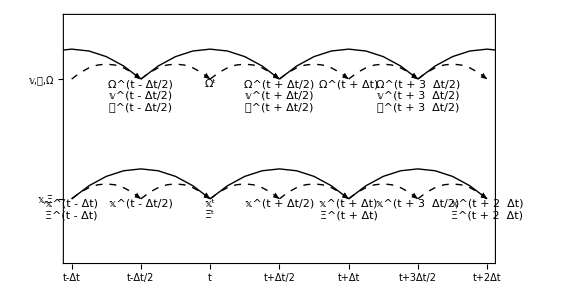

```mathematica
With[{},Graphics[{
Text[#2,{#,1.5},{0,1}]&@@@Thread[{Range[-1/2,3/2,1/2],{"Ω^(t - Δt/2)\n𝕧^(t - Δt/2)\n𝒥^(t - Δt/2)","Ω^t","Ω^(t + Δt/2)\n𝕧^(t + Δt/2)\n𝒥^(t + Δt/2)","Ω^(t + Δt)","Ω^(t + 3  Δt/2)\n𝕧^(t + 3  Δt/2)\n𝒥^(t + 3  Δt/2)"}}],
Text[#2,{#,.5},{0,1}]&@@@Thread[{Range[-1,2,1/2],{"𝕩^(t - Δt)\nΞ^(t - Δt)","𝕩^(t - Δt/2)","𝕩^t\nΞ^t","𝕩^(t + Δt/2)","𝕩^(t + Δt)\nΞ^(t + Δt)","𝕩^(t + 3  Δt/2)","𝕩^(t + 2  Δt)\nΞ^(t + 2  Δt)"}}],
{Arrowheads[{{Medium,.55}}],Arrow@BezierCurve[{{#,1.5},{#+.5,2},{#+1,1.5}}]&/@(Range[-1,2]-.5),Arrow@BezierCurve[{{#,.5},{#+.5,1},{#+1,.5}}]&/@Range[-1,1]},
{Dashed,Arrowheads[{{Medium,.55}}],Arrow@BezierCurve[{{#,1.5},{#+.25,1.75},{#+.5,1.5}}]&/@(Range[-1,3/2,1/2]),Arrow@BezierCurve[{{#,.5},{#+.25,.75},{#+.5,.5}}]&/@Range[-1,3/2,1/2]}
},PlotRange->{{-1,2},{0,2}},Frame->{{True,False},{True,False}},FrameTicks->{{{{.5,"𝕩,Ξ"},{1.5,"𝕧,𝒥,Ω"}},None},{{{-1,"t-Δt"},{-1/2,"t-Δt/2"},{0,"t"},{1/2,"t+Δt/2"},{1,"t+Δt"},{3/2,"t+3Δt/2"},{2,"t+2Δt"}},None}},ImageSize->Large,AspectRatio->1/2,GridLines->{Range[-1,2,1/2],{.5,1.5}},GridLinesStyle->Directive[Dotted,Gray],PlotRangePadding->Scaled[.04],PlotRangeClipping->True,BaseStyle->15]]
```

### Cycling (Modified)

1. Advance Ω^(t-Δt/2) by Δt/2 to Ω^t using Ξ^t.
2. Advance 𝕧^(t-Δt/2) to 𝕧^(t+Δt/2) using 𝕩^t, Ω^t, and Ξ^t. 
2.1 Advance 𝕍_f^(t-Δt/2) to 𝕍_f^(t+Δt/2) using Ω^t and Ξ^t.
2.2 Advance δn_f^t to δn_f^(t+Δt) using 𝕍_f^(t+Δt/2).
3. Advance Ω^t by another Δt/2 to Ω^(t+Δt/2) using Ξ^t.
4. Collect 𝒥^- from the particle positions 𝕩^t and velocities 𝕧^(t+Δt/2).
5. Advance 𝕩^t by Δt to 𝕩^(t+Δt) using 𝕧^(t+Δt/2).
6. Collect 𝒥^+ from the particle positions 𝕩^(t+Δt) and velocities 𝕧^(t+Δt/2), and calculate 𝒥^(t+Δt/2)=(𝒥^-+𝒥^+)/2.
6.1 Collect 𝒥^(t+Δt/2) from 𝕍_f^(t+Δt/2).
7. Advance Ξ^t to Ξ^(t+Δt) using Ω^(t+Δt/2) and 𝒥^(t+Δt/2).

```mathematica
With[{},Graphics[{
Text[#2,{#,1.5},{0,1}]&@@@Thread[{Range[-1/2,3/2,1/2],{"Ω^(t - Δt/2)\n𝕧^(t - Δt/2)\n𝒥^(t - Δt/2)","Ω^t","Ω^(t + Δt/2)\n𝕧^(t + Δt/2)\n𝒥^(t + Δt/2)","Ω^(t + Δt)","Ω^(t + 3  Δt/2)\n𝕧^(t + 3  Δt/2)\n𝒥^(t + 3  Δt/2)"}}],
Text[#2,{#,.5},{0,1}]&@@@Thread[{Range[-1,2,1/2],{"𝕩^(t - Δt)\nΞ^(t - Δt)","𝕩^(t - Δt/2)","𝕩^t\nΞ^t","𝕩^(t + Δt/2)","𝕩^(t + Δt)\nΞ^(t + Δt)","𝕩^(t + 3  Δt/2)","𝕩^(t + 2  Δt)\nΞ^(t + 2  Δt)"}}],
{Arrowheads[{{Medium,.55}}],Arrow@BezierCurve[{{#,1.5},{#+.5,2},{#+1,1.5}}]&/@(Range[-1,2]-.5),Arrow@BezierCurve[{{#,.5},{#+.5,1},{#+1,.5}}]&/@Range[-1,1]},
{Dashed,Arrowheads[{{Medium,.55}}],Arrow@BezierCurve[{{#,1.5},{#+.25,1.75},{#+.5,1.5}}]&/@(Range[-1,3/2,1/2]),Arrow@BezierCurve[{{#,.5},{#+.25,.75},{#+.5,.5}}]&/@Range[-1,3/2,1/2]}
},PlotRange->{{-1,2},{0,2}},Frame->{{True,False},{True,False}},FrameTicks->{{{{.5,"𝕩,Ξ"},{1.5,"𝕧,𝒥,Ω"}},None},{{{-1,"t-Δt"},{-1/2,"t-Δt/2"},{0,"t"},{1/2,"t+Δt/2"},{1,"t+Δt"},{3/2,"t+3Δt/2"},{2,"t+2Δt"}},None}},ImageSize->Large,AspectRatio->1/2,GridLines->{Range[-1,2,1/2],{.5,1.5}},GridLinesStyle->Directive[Dotted,Gray],PlotRangePadding->Scaled[.04],PlotRangeClipping->True,BaseStyle->15]]
```

-Graphics-

## Discretization

Maxwells equations:
(∂Ξ^1/∂t
∂Ξ^2/∂t
∂Ξ^3/∂t)=c/(√g)(∂Ω_3/∂x^2-∂Ω_2/∂x^3
∂Ω_1/∂x^3-∂Ω_3/∂x^1
∂Ω_2/∂x^1-∂Ω_1/∂x^2)-(𝒥^1
𝒥^2
𝒥^3),
(∂Ω^1/∂t
∂Ω^2/∂t
∂Ω^3/∂t)=-c/(√g)(∂Ξ_3/∂x^2-∂Ξ_2/∂x^3
∂Ξ_1/∂x^3-∂Ξ_3/∂x^1
∂Ξ_2/∂x^1-∂Ξ_1/∂x^2),
c(∂Ξ^1/∂x^1+∂Ξ^2/∂x^2+∂Ξ^3/∂x^3)+c/(√g)(Ξ^1∂√g/∂x^1+Ξ^2∂√g/∂x^2+Ξ^3∂√g/∂x^3)=Π,
c(∂Ω^1/∂x^1+∂Ω^2/∂x^2+∂Ω^3/∂x^3)+c/(√g)(Ω^1∂√g/∂x^1+Ω^2∂√g/∂x^2+Ω^3∂√g/∂x^3)=0.

Continuity equation:
c(∂𝒥^1/∂x^1+∂𝒥^2/∂x^2+∂𝒥^3/∂x^3)+c/(√g)(𝒥^1∂√g/∂x^1+𝒥^2∂√g/∂x^2+𝒥^3∂√g/∂x^3)+∂Π/∂t=0.

Equations of motion (non-relativistic):
(∂x^1/∂t
∂x^2/∂t
∂x^3/∂t)=(v^1
v^2
v^3),
(∂v_x/∂t
∂v_y/∂t
∂v_z/∂t)=Ω_s/Ω_0(c Ξ_x+v_y Ω_z-v_z Ω_y
c Ξ_y+v_z Ω_x-v_x Ω_z
c Ξ_z+v_x Ω_y-v_y Ω_x).

Cold fluid:
(∂(δn_f/n_(f,0)))/(∂t)=-1/(√g)∂/(∂x^i)√g V_f^i.

4th-order accurate differencing scheme for spatial derivatives:
(∂u_j)/(∂x)=1/(12Δx)(u_(j-2)-8 u_(j-1)+8 u_(j+1)-u_(j+2)).

### 1D in x^1 coordinate

#### Grid: Staggered

Cell center quantities: Ξ⃗, 𝒥⃗, all discrete particle moments, and 𝕍_f.
Cell corner quantities: Ω⃗ and δn_f.

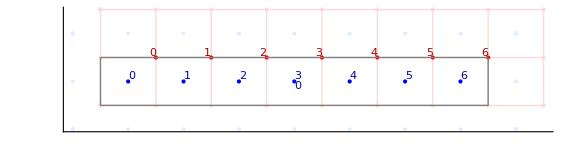

```mathematica
With[{ξ=0.,Δ1=1,Δ2=1,q1max=4,q2max=1},
If[ξ Δ1 q1max≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[-q1max,q1max]Δ1;
Δ2q2=Range[-q2max,q2max]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Plus[Δ2q2,+.5]Cos[ξ#]^2}]&/@Plus[Δ1q1,+.5];
Legended[
Graphics[{
(*{LightBlue,Thickness[Medium],Line/@xyF,Line/@Thread[xyF]},*)
{LightRed,Thickness[Medium],Line/@xyH,Line/@Thread[xyH]},
{Red,PointSize[Medium],Point/@xyH[[2;;-2,2;;-2]]},
{LightRed,PointSize[Medium],Point[First[xyH]],Point[First/@xyH],Point[Last[xyH]],Point[Last/@xyH]},
{Blue,PointSize[Medium],Point/@xyF[[2;;-2,2;;-2]]},
{LightBlue,PointSize[Medium],Point[First[xyF]],Point[First/@xyF],Point[Last[xyF]],Point[Last/@xyF]},
{Gray,Thickness[Medium],Line[First[xyH]//Most],Line[First/@xyH//Most],Line[Part[xyH,-2]//Most],Line[Part[xyH,All,-2]//Most]},
{Darker@Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,xyF[[2;;-2,q2max+1]]],MapIndexed[Text[First[#2]-1,#,{-1,1}]&,xyF[[q1max+1,2;;-2]]]},
{Darker@Red,MapIndexed[Text[First[#2]-1,#,{1,-1}]&,xyH[[2;;-2,q2max+1]]]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->{True,False},
Ticks->False,
BaseStyle->11,
ImageSize->Large
],
Placed[PointLegend[{LightRed,Gray,Red,Blue,Gray},{"Cell Boundary","Particle Boundary","Cell Corner","Cell Center","Ghost Cells"},Joined->{True,True,False,False,False},LegendLayout->(Row[Join@@#,Spacer[2]]&)],Above]
]
]
]
```

#### Grid: Collocated

Grid points are located in cell centers.

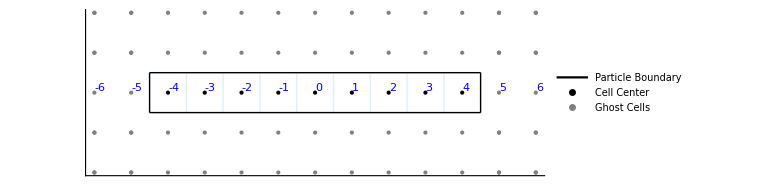

```mathematica
With[{ξ=0,Δ1=1,Δ2=1,q1max=4+2,q2max=0+2},
If[ξ Δ1 q1max≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[-q1max,q1max]Δ1;
Δ2q2=Range[-q2max,q2max]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],MovingAverage[Δ2q2,2]Cos[ξ#]^2}]&/@MovingAverage[Δ1q1,2];
Legended[
Graphics[{
{LightBlue,Thickness[Medium],Line/@xyH[[2;;-2,2;;-2]],Line/@Thread[xyH[[2;;-2,2;;-2]]]},
{Black,PointSize[Medium],Point/@xyF[[3;;-3,3;;-3]]},
{Gray,PointSize[Medium],Point/@xyF[[1;;2]],Point/@xyF[[All,1;;2]],Point/@xyF[[-2;;-1]],Point/@xyF[[All,-2;;-1]]},
{Blue,MapIndexed[Text[First[#2]-1-q1max,#,{-1,-1}]&,xyF[[All,q2max+1]]]},
{Black,Thickness[Medium],Line[xyH[[2;;-2,2]]],Line[xyH[[-2,2;;-2]]],Line[xyH[[2;;-2,-2]]],Line[xyH[[2,2;;-2]]]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->{True,False},
Ticks->False,
BaseStyle->11,
ImageSize->Large
],
Placed[PointLegend[{Black,Black,Gray},{"Particle Boundary","Cell Center","Ghost Cells"},Joined->{True,False,False},LegendLayout->"Row"],Above]
]
]
]
```

#### Magnetic field update

Staggered grid:
(ΔΩ^1/Δt
ΔΩ^2/Δt
ΔΩ^3/Δt)=-c/(√g)(0
-ΔΞ_3^t/Δx^1
+ΔΞ_2^t/Δx^1) ⇒ 
(Ω_(t+Δt/2)^(1;i)
Ω_(t+Δt/2)^(2;i)
Ω_(t+Δt/2)^(3;i))=(Ω_(t-Δt/2)^(1;i)
Ω_(t-Δt/2)^(2;i)
Ω_(t-Δt/2)^(3;i))-(c Δt)/(√g Δx^1)(0
-(Ξ_(3;i+1)^t-Ξ_(3;i)^t)
+(Ξ_(2;i+1)^t-Ξ_(2;i)^t))

Collocated grid:
(ΔΩ^1/Δt
ΔΩ^2/Δt
ΔΩ^3/Δt)=-c/(√g)(0
-ΔΞ_3^t/Δx^1
+ΔΞ_2^t/Δx^1) ⇒ 
(Ω_(t+Δt/2)^(1;i)
Ω_(t+Δt/2)^(2;i)
Ω_(t+Δt/2)^(3;i))=(Ω_(t-Δt/2)^(1;i)
Ω_(t-Δt/2)^(2;i)
Ω_(t-Δt/2)^(3;i))-(c Δt/√g)/(12 Δx^1)(0
-(Ξ_(3;i-2)^t-8 Ξ_(3;i-1)^t+8 Ξ_(3;i+1)^t-Ξ_(3;i+2)^t)
+(Ξ_(2;i-2)^t-8 Ξ_(2;i-1)^t+8 Ξ_(2;i+1)^t-Ξ_(2;i+2)^t))

After update, calculate covariant components:
Ω_i=Ω^j g_ij;
(Ω_1
Ω_2
Ω_3)=(g_11 Ω^1+g_12 Ω^2+g_13 Ω^3
g_21 Ω^1+g_22 Ω^2+g_23 Ω^3
g_31 Ω^1+g_32 Ω^2+g_33 Ω^3);
and cartesian components:
(Ω_x
Ω_y
Ω_z)=(Ω^1(g⃗)_1·(ê)_x+Ω^2(g⃗)_2·(ê)_x+Ω^3(g⃗)_3·(ê)_x
Ω^1(g⃗)_1·(ê)_y+Ω^2(g⃗)_2·(ê)_y+Ω^3(g⃗)_3·(ê)_y
Ω^1(g⃗)_1·(ê)_z+Ω^2(g⃗)_2·(ê)_z+Ω^3(g⃗)_3·(ê)_z)

#### Electric field update

Staggered grid:
(ΔΞ^1/Δt
ΔΞ^2/Δt
ΔΞ^3/Δt)=c/(√g)(0
-ΔΩ_3^(t+Δt/2)/Δx^1
+ΔΩ_2^(t+Δt/2)/Δx^1)-(𝒥_(t+Δt/2)^1
𝒥_(t+Δt/2)^2
𝒥_(t+Δt/2)^3) ⇒ 
(Ξ_(t+Δt)^(1;i)
Ξ_(t+Δt)^(2;i)
Ξ_(t+Δt)^(3;i))=(Ξ_t^(1;i)
Ξ_t^(2;i)
Ξ_t^(3;i))-Δt(𝒥_(t+Δt/2)^(1;i)
𝒥_(t+Δt/2)^(2;i)
𝒥_(t+Δt/2)^(3;i))+(c Δt)/(√g Δx^1)(0
-(Ω_(3;i)^(t+Δt/2)-Ω_(3;i-1)^(t+Δt/2))
+(Ω_(2;i)^(t+Δt/2)-Ω_(2;i-1)^(t+Δt/2)))

Collocated grid:
(ΔΞ^1/Δt
ΔΞ^2/Δt
ΔΞ^3/Δt)=c/(√g)(0
-ΔΩ_3^(t+Δt/2)/Δx^1
+ΔΩ_2^(t+Δt/2)/Δx^1)-(𝒥_(t+Δt/2)^1
𝒥_(t+Δt/2)^2
𝒥_(t+Δt/2)^3) ⇒ 
(Ξ_(t+Δt)^(1;i)
Ξ_(t+Δt)^(2;i)
Ξ_(t+Δt)^(3;i))=(Ξ_t^(1;i)
Ξ_t^(2;i)
Ξ_t^(3;i))-Δt(𝒥_(t+Δt/2)^(1;i)
𝒥_(t+Δt/2)^(2;i)
𝒥_(t+Δt/2)^(3;i))+(c Δt/√g)/(12 Δx^1)(0
-(Ω_(3;i-2)^(t+Δt/2)-8 Ω_(3;i-1)^(t+Δt/2)+8 Ω_(3;i+1)^(t+Δt/2)-Ω_(3;i+2)^(t+Δt/2))
+(Ω_(2;i-2)^(t+Δt/2)-8 Ω_(2;i-1)^(t+Δt/2)+8 Ω_(2;i+1)^(t+Δt/2)-Ω_(2;i+2)^(t+Δt/2)))

After update, calculate covariant components:
Ξ_i=Ξ^j g_ij;
(Ξ_1
Ξ_2
Ξ_3)=(g_11 Ξ^1+g_12 Ξ^2+g_13 Ξ^3
g_21 Ξ^1+g_22 Ξ^2+g_23 Ξ^3
g_31 Ξ^1+g_32 Ξ^2+g_33 Ξ^3);
and cartesian components:
(Ξ_x
Ξ_y
Ξ_z)=(Ξ^1(g⃗)_1·(ê)_x+Ξ^2(g⃗)_2·(ê)_x+Ξ^3(g⃗)_3·(ê)_x
Ξ^1(g⃗)_1·(ê)_y+Ξ^2(g⃗)_2·(ê)_y+Ξ^3(g⃗)_3·(ê)_y
Ξ^1(g⃗)_1·(ê)_z+Ξ^2(g⃗)_2·(ê)_z+Ξ^3(g⃗)_3·(ê)_z)

#### Cold fluid update

Staggered grid:
(Δ(δn_f/n_(f,0)))/Δt=-1/(√g)((Δ(√g V_(f;t+Δt/2)^1))/Δx^1) ⇒ 
(δn_(f;i)^(t+Δt))/(n_(f,0))=(δn_(f;i)^t)/(n_(f,0))-(2Δt)/((√(g_(i+1))+√g_i)Δx^1)(√(g_(i+1))V_(f;t+Δt/2)^(1;i+1)-√g_i V_(f;t+Δt/2)^(1;i))

Collocated grid:
(Δ(δn_f/n_(f,0)))/Δt=-1/(√g)((Δ(√g V_(f;t+Δt/2)^1))/Δx^1) ⇒ 
(δn_(f;i)^(t+Δt))/(n_(f,0))=(δn_(f;i)^t)/(n_(f,0))-(Δt/√g_i)/(12 Δx^1)(√(g_(i-2))V_(f;t+Δt/2)^(1;i-2)-8 √(g_(i-1))V_(f;t+Δt/2)^(1;i-1)+8 √(g_(i+1))V_(f;t+Δt/2)^(1;i+1)-√(g_(i+2))V_(f;t+Δt/2)^(1;i+2))

#### Position update

Cartesian to curvilinear:
(v^1
v^2
v^3)=(v_x(ê)_x·(g⃗)^1+v_y(ê)_y·(g⃗)^1+v_z(ê)_z·(g⃗)^1
v_x(ê)_x·(g⃗)^2+v_y(ê)_y·(g⃗)^2+v_z(ê)_z·(g⃗)^2
v_x(ê)_x·(g⃗)^3+v_y(ê)_y·(g⃗)^3+v_z(ê)_z·(g⃗)^3)

x_(t+Δt)^1=x_t^1+Δt v_(t+Δt/2)^1.

#### Velocity update in cartesian coordinate

Step 0 - (Ξ_x[x_t^1]
Ξ_y[x_t^1]
Ξ_z[x_t^1])=∑_(i,j) (Ξ_(x;i)^t
Ξ_(y;i)^t
Ξ_(z;i)^t)S[x_t^1-x^(1;i)] and (Ω_x[x_t^1]
Ω_y[x_t^1]
Ω_z[x_t^1])=(Ω_x^0[x_t^1]
Ω_y^0[x_t^1]
Ω_z^0[x_t^1])+∑_i (δΩ_(x;i)^t
δΩ_(y;i)^t
δΩ_(z;i)^t)S[x_t^1-Δx^1/2-x^(1;i)],
Step 1 - (v_x^-
v_y^-
v_z^-)=(v_x^(t-Δt/2)
v_y^(t-Δt/2)
v_z^(t-Δt/2))+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t),
Step 2 - (v_x^0
v_y^0
v_z^0)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2(v_y^-Ω_z^t-v_z^-Ω_y^t
v_z^-Ω_x^t-v_x^-Ω_z^t
v_x^-Ω_y^t-v_y^-Ω_x^t),
Step 3 - (v_x^+
v_y^+
v_z^+)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2 2/(1+(Ω_s/Ω_0 Δt/2)^2((Ω_x^t)^2+(Ω_y^t)^2+(Ω_z^t)^2))(v_y^0 Ω_z^t-v_z^0 Ω_y^t
v_z^0 Ω_x^t-v_x^0 Ω_z^t
v_x^0 Ω_y^t-v_y^0 Ω_x^t), and
Step 4 - (v_x^(t+Δt/2)
v_y^(t+Δt/2)
v_z^(t+Δt/2))=(v_x^+
v_y^+
v_z^+)+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t).

#### Moments: from particle to grid

Number density (zeroth velocity moment) at ith grid point:
n_(t;s)^i=n_(0;s)^i(∑_p S[x_(t;s)^(1;p)-x^(1;i)])/(N_(c;s)^(0;i))=n_(0;s)(∑_p S[x_(t;s)^(1;p)-x^(1;i)])/(N_(c;s)), where N_(c;s)^0 is the initial number of simulation particles of species s at a reference cell; n_(0;s) is the initial number density of the species s at that cell; N_(c;s)^(0;i) is the initial number of simulation particles at (q^i) cell; and n_(0;s)^i is the initial number density at (q^i) cell.
Charge density at (q^i) cell is:
Π_t^i=∑_s Ω_0/Ω_s ω_(s;i)^2(∑_p S[x_(t;s)^(1;p)-x^(1;i)])/(N_(c;s)^(0;i))=∑_s Ω_0/Ω_s ω_(s;0)^2(∑_p S[x_(t;s)^(1;p)-x^(1;i)])/(N_(c;s)^0)=∑_s Ω_0/Ω_s ω_(s;0)^2(n_(t;s)^i)/(n_(0;s)),
where ω_(s;0) is the initial plasma frequency at the reference cell; and ω_(s;i)^2 is the initial plasma frequency at (q^i) cell.

```mathematica
With[{Nc=100,Nx=2,n0=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{x},
x=RandomReal[{0,1},Nc*Nx];
(Plus@@@S[x])/Nc
]]
```

Average flow speed weighted by n_(t;s)^i/n_(0;s):
(V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))=∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^0)
Average flow speed is given by (V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))/(n_(t;s)^i)/(n_(0;s)).
Current density:
(𝒥_(x;i)^(t;s)
𝒥_(y;i)^(t;s)
𝒥_(z;i)^(t;s))=Ω_0/Ω_s(ω_(s;i)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^(0;i))=Ω_0/Ω_s(ω_(s;0)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^0)=Ω_0/Ω_s(ω_(s;0)^2)/c(V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))
Cartesian to curvilinear:
(𝒥^1
𝒥^2
𝒥^3)=(𝒥_x(ê)_x·(g⃗)^1+𝒥_y(ê)_y·(g⃗)^1+𝒥_z(ê)_z·(g⃗)^1
𝒥_x(ê)_x·(g⃗)^2+𝒥_y(ê)_y·(g⃗)^2+𝒥_z(ê)_z·(g⃗)^2
𝒥_x(ê)_x·(g⃗)^3+𝒥_y(ê)_y·(g⃗)^3+𝒥_z(ê)_z·(g⃗)^3)

```mathematica
Clear[icdf];
icdf:=icdf=With[{cdf=Function[v,-(2 ⅇ^(-v^2) v)/(√π)+Erf[v]],n=1000,vmax=4.},Interpolation[Table[{cdf[vmax i/n],vmax i/n},{i,0,n}]]]
```

```mathematica
Plot[icdf[i],{i,0,1},PlotRange->All]
```

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
TableForm[Function[v,{v//Mean,Mean[(Total[v#]&/@S[x])/Nc]n0}]/@{vx,vy,vz},TableHeadings->{{"v_x","v_y","v_z"},{"⟨𝕧⟩","2nd Mom × n_s^0"}}]
]]
```

Average second velocity moment weighted by n_(t;s)^i/n_(0;s):
(2 𝕨_s)/m_s=⟨𝕧_i^(t;s)𝕧_i^(t;s)⟩=n_(0;s)^i∑_p 𝕧_p^(t;s)𝕧_p^(t;s)S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^(0;i))=n_(0;s)∑_p 𝕧_p^(t;s)𝕧_p^(t;s)S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^0).
Kinetic energy density (equivalent to pressure):
ε_i^(t;s)=Ω_0^2/Ω_s^2(ω_(s;i)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^(0;i))=Ω_0^2/Ω_s^2(ω_(s;0)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^0).
Thermal speed squared:
⟨(Δv_(x,s;i)^2
Δv_(y,s;i)^2
Δv_(z,s;i)^2)⟩=(n_(0;s))/(n_(t;s)^i)(∑_p (v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)S[x_(t;s)^(1;p)-x^(1;i)]/(N_(c;s)^0)-(V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))^2/(n_(t;s)^i)/(n_(0;s))).

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
{Total[Flatten[{vx,vy,vz}^2]]/2,
Total[Total[(vx^2+vy^2+vz^2)#/2]/Nc&/@S[x]]*Nc}
]]
```

### 2D in x^1-x^2 plane

#### Grid: Staggered

Cell center quantities: Ξ⃗, 𝒥⃗, all discrete particle moments, and 𝕍_f.
Cell corner quantities: Ω⃗ and δn_f.

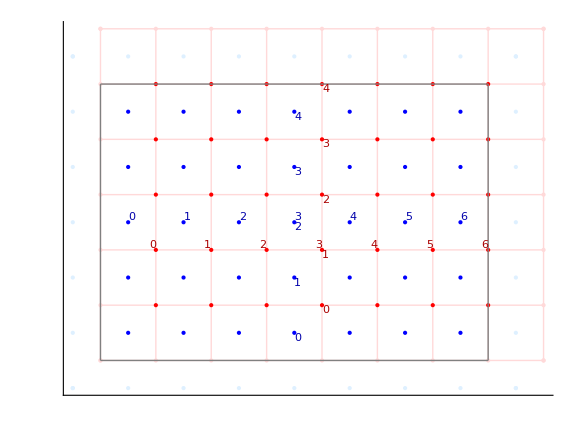

```mathematica
With[{ξ=.0,Δ1=1,Δ2=1,q1max=4,q2max=3},
If[ξ Δ1 q1max≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[-q1max,q1max]Δ1;
Δ2q2=Range[-q2max,q2max]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Plus[Δ2q2,+.5]Cos[ξ#]^2}]&/@Plus[Δ1q1,+.5];
Legended[
Graphics[{
(*{LightBlue,Thickness[Medium],Line/@xyF,Line/@Thread[xyF]},*)
{LightRed,Thickness[Medium],Line/@xyH,Line/@Thread[xyH]},
{Red,PointSize[Medium],Point/@xyH[[2;;-2,2;;-2]]},
{LightRed,PointSize[Medium],Point[First[xyH]],Point[First/@xyH],Point[Last[xyH]],Point[Last/@xyH]},
{Blue,PointSize[Medium],Point/@xyF[[2;;-2,2;;-2]]},
{LightBlue,PointSize[Medium],Point[First[xyF]],Point[First/@xyF],Point[Last[xyF]],Point[Last/@xyF]},
{Gray,Thickness[Medium],Line[First[xyH]//Most],Line[First/@xyH//Most],Line[Part[xyH,-2]//Most],Line[Part[xyH,All,-2]//Most]},
{Darker@Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,xyF[[2;;-2,q2max+1]]],MapIndexed[Text[First[#2]-1,#,{-1,1}]&,xyF[[q1max+1,2;;-2]]]},
{Darker@Red,MapIndexed[Text[First[#2]-1,#,{1,-1}]&,xyH[[2;;-2,q2max]]],MapIndexed[Text[First[#2]-1,#,{-1,1}]&,xyH[[q1max+1,2;;-2]]]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->True,
Ticks->False,
BaseStyle->11,
ImageSize->Large
],
Placed[PointLegend[{LightRed,Gray,Red,Blue,Gray},{"Cell Boundary","Particle Boundary","Cell Corner","Cell Center","Ghost Cells"},Joined->{True,True,False,False,False},LegendLayout->(Row[Join@@#,Spacer[2]]&)],Above]
]
]
]
```

#### Grid: Collocated

Grid points are located in cell centers.

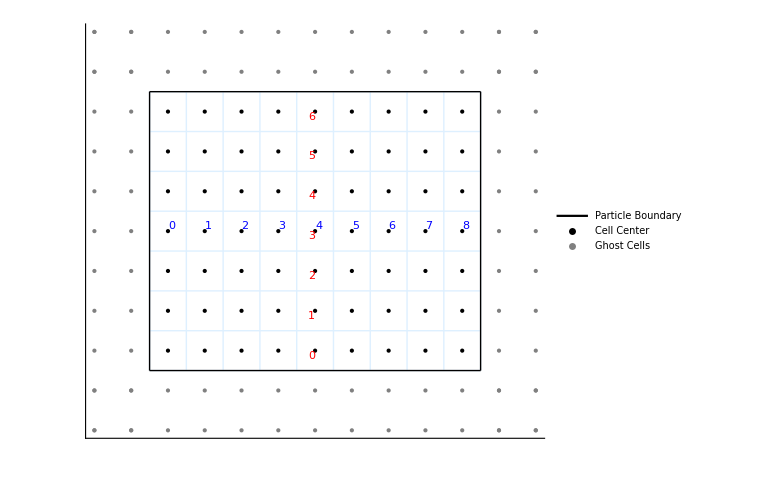

```mathematica
With[{ξ=.0,Δ1=1,Δ2=1,q1max=4+2,q2max=3+2},
If[ξ Δ1 q1max≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[-q1max,q1max]Δ1;
Δ2q2=Range[-q2max,q2max]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],MovingAverage[Δ2q2,2]Cos[ξ#]^2}]&/@MovingAverage[Δ1q1,2];
Legended[
Graphics[{
{LightBlue,Thickness[Medium],Line/@xyH[[2;;-2,2;;-2]],Line/@Thread[xyH[[2;;-2,2;;-2]]]},
{Black,PointSize[Medium],Point/@xyF[[3;;-3,3;;-3]]},
{Gray,PointSize[Medium],Point/@xyF[[1;;2]],Point/@xyF[[All,1;;2]],Point/@xyF[[-2;;-1]],Point/@xyF[[All,-2;;-1]]},
{Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,xyF[[3;;-3,q2max+1]]]},
{Red,MapIndexed[Text[First[#2]-1,#,{1,1}]&,xyF[[q1max+1,3;;-3]]]},
{Black,Thickness[Medium],Line[xyH[[2;;-2,2]]],Line[xyH[[-2,2;;-2]]],Line[xyH[[2;;-2,-2]]],Line[xyH[[2,2;;-2]]]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->True,
Ticks->False,
BaseStyle->11,
ImageSize->Large
],
Placed[PointLegend[{Black,Black,Gray},{"Particle Boundary","Cell Center","Ghost Cells"},Joined->{True,False,False},LegendLayout->"Row"],Above]
]
]
]
```

#### Magnetic field update

Staggered grid:
(ΔΩ^1/Δt
ΔΩ^2/Δt
ΔΩ^3/Δt)=-c/(√g)(ΔΞ_3^t/Δx^2
-ΔΞ_3^t/Δx^1
ΔΞ_2^t/Δx^1-ΔΞ_1^t/Δx^2) ⇒ 
(Ω_(t+Δt/2)^(1;i,j)
Ω_(t+Δt/2)^(2;i,j)
Ω_(t+Δt/2)^(3;i,j))=(Ω_(t-Δt/2)^(1;i,j)
Ω_(t-Δt/2)^(2;i,j)
Ω_(t-Δt/2)^(3;i,j))-(c Δt)/(2 √g Δx^1)(0
-((Ξ_(3;i+1,j+1)^t+Ξ_(3;i+1,j)^t)-(Ξ_(3;i,j+1)^t+Ξ_(3;i,j)^t))
+((Ξ_(2;i+1,j+1)^t+Ξ_(2;i+1,j)^t)-(Ξ_(2;i,j+1)^t+Ξ_(2;i,j)^t)))-(c Δt)/(2 √g Δx^2)(+((Ξ_(3;i+1,j+1)^t+Ξ_(3;i,j+1)^t)-(Ξ_(3;i+1,j)^t+Ξ_(3;i,j)^t))
0
-((Ξ_(1;i+1,j+1)^t+Ξ_(1;i,j+1)^t)-(Ξ_(1;i+1,j)^t+Ξ_(1;i,j)^t)))

Collocated grid:
(ΔΩ^1/Δt
ΔΩ^2/Δt
ΔΩ^3/Δt)=-c/(√g)(ΔΞ_3^t/Δx^2
-ΔΞ_3^t/Δx^1
ΔΞ_2^t/Δx^1-ΔΞ_1^t/Δx^2) ⇒ 
(Ω_(t+Δt/2)^(1;i,j)
Ω_(t+Δt/2)^(2;i,j)
Ω_(t+Δt/2)^(3;i,j))=(Ω_(t-Δt/2)^(1;i,j)
Ω_(t-Δt/2)^(2;i,j)
Ω_(t-Δt/2)^(3;i,j))-(c Δt/√g)/(12 Δx^1)(0
-(Ξ_(3;i-2,j)^t-8 Ξ_(3;i-1,j)^t+8 Ξ_(3;i+1,j)^t-Ξ_(3;i+2,j)^t)
+(Ξ_(2;i-2,j)^t-8 Ξ_(2;i-1,j)^t+8 Ξ_(2;i+1,j)^t-Ξ_(2;i+2,j)^t))-(c Δt/√g)/(12 Δx^2)(+(Ξ_(3;i,j-2)^t-8 Ξ_(3;i,j-1)^t+8 Ξ_(3;i,j+1)^t-Ξ_(3;i,j+2)^t)
0
-(Ξ_(1;i,j-2)^t-8 Ξ_(1;i,j-1)^t+8 Ξ_(1;i,j+1)^t-Ξ_(1;i,j+2)^t))

After update, calculate covariant components:
Ω_i=Ω^j g_ij;
(Ω_1
Ω_2
Ω_3)=(g_11 Ω^1+g_12 Ω^2+g_13 Ω^3
g_21 Ω^1+g_22 Ω^2+g_23 Ω^3
g_31 Ω^1+g_32 Ω^2+g_33 Ω^3);
and cartesian components:
(Ω_x
Ω_y
Ω_z)=(Ω^1(g⃗)_1·(ê)_x+Ω^2(g⃗)_2·(ê)_x+Ω^3(g⃗)_3·(ê)_x
Ω^1(g⃗)_1·(ê)_y+Ω^2(g⃗)_2·(ê)_y+Ω^3(g⃗)_3·(ê)_y
Ω^1(g⃗)_1·(ê)_z+Ω^2(g⃗)_2·(ê)_z+Ω^3(g⃗)_3·(ê)_z)

#### Electric field update

Staggered grid:
(ΔΞ^1/Δt
ΔΞ^2/Δt
ΔΞ^3/Δt)=c/(√g)(ΔΩ_3^(t+Δt/2)/Δx^2
-ΔΩ_3^(t+Δt/2)/Δx^1
ΔΩ_2^(t+Δt/2)/Δx^1-ΔΩ_1^(t+Δt/2)/Δx^2)-(𝒥_(t+Δt/2)^1
𝒥_(t+Δt/2)^2
𝒥_(t+Δt/2)^3) ⇒ 
(Ξ_(t+Δt)^(1;i,j)
Ξ_(t+Δt)^(2;i,j)
Ξ_(t+Δt)^(3;i,j))=(Ξ_t^(1;i,j)
Ξ_t^(2;i,j)
Ξ_t^(3;i,j))-Δt(𝒥_(t+Δt/2)^(1;i,j)
𝒥_(t+Δt/2)^(2;i,j)
𝒥_(t+Δt/2)^(3;i,j))+(c Δt)/(2 √g Δx^1)(0
-((Ω_(3;i,j)^(t+Δt/2)+Ω_(3;i,j-1)^(t+Δt/2))-(Ω_(3;i-1,j)^(t+Δt/2)+Ω_(3;i-1,j-1)^(t+Δt/2)))
+((Ω_(2;i,j)^(t+Δt/2)+Ω_(2;i,j-1)^(t+Δt/2))-(Ω_(2;i-1,j)^(t+Δt/2)+Ω_(2;i-1,j-1)^(t+Δt/2))))+(c Δt)/(2 √g Δx^2)(+((Ω_(3;i,j)^(t+Δt/2)+Ω_(3;i-1,j)^(t+Δt/2))-(Ω_(3;i,j-1)^(t+Δt/2)+Ω_(3;i-1,j-1)^(t+Δt/2)))
0
-((Ω_(1;i,j)^(t+Δt/2)+Ω_(1;i-1,j)^(t+Δt/2))-(Ω_(1;i,j-1)^(t+Δt/2)+Ω_(1;i-1,j-1)^(t+Δt/2))))

Collocated grid:
(ΔΞ^1/Δt
ΔΞ^2/Δt
ΔΞ^3/Δt)=c/(√g)(ΔΩ_3^(t+Δt/2)/Δx^2
-ΔΩ_3^(t+Δt/2)/Δx^1
ΔΩ_2^(t+Δt/2)/Δx^1-ΔΩ_1^(t+Δt/2)/Δx^2)-(𝒥_(t+Δt/2)^1
𝒥_(t+Δt/2)^2
𝒥_(t+Δt/2)^3) ⇒ 
(Ξ_(t+Δt)^(1;i,j)
Ξ_(t+Δt)^(2;i,j)
Ξ_(t+Δt)^(3;i,j))=(Ξ_t^(1;i,j)
Ξ_t^(2;i,j)
Ξ_t^(3;i,j))-Δt(𝒥_(t+Δt/2)^(1;i,j)
𝒥_(t+Δt/2)^(2;i,j)
𝒥_(t+Δt/2)^(3;i,j))+(c Δt/√g)/(12 Δx^1)(0
-(Ω_(3;i-2,j)^(t+Δt/2)-8 Ω_(3;i-1,j)^(t+Δt/2)+8 Ω_(3;i+1,j)^(t+Δt/2)-Ω_(3;i+2,j)^(t+Δt/2))
+(Ω_(2;i-2,j)^(t+Δt/2)-8 Ω_(2;i-1,j)^(t+Δt/2)+8 Ω_(2;i+1,j)^(t+Δt/2)-Ω_(2;i+2,j)^(t+Δt/2)))+(c Δt/√g)/(12 Δx^2)(+(Ω_(3;i,j-2)^(t+Δt/2)-8 Ω_(3;i,j-1)^(t+Δt/2)+8 Ω_(3;i,j+1)^(t+Δt/2)-Ω_(3;i,j+2)^(t+Δt/2))
0
-(Ω_(1;i,j-2)^(t+Δt/2)-8 Ω_(1;i,j-1)^(t+Δt/2)+8 Ω_(1;i,j+1)^(t+Δt/2)-Ω_(1;i,j+2)^(t+Δt/2)))

After update, calculate covariant components:
Ξ_i=Ξ^j g_ij;
(Ξ_1
Ξ_2
Ξ_3)=(g_11 Ξ^1+g_12 Ξ^2+g_13 Ξ^3
g_21 Ξ^1+g_22 Ξ^2+g_23 Ξ^3
g_31 Ξ^1+g_32 Ξ^2+g_33 Ξ^3);
and cartesian components:
(Ξ_x
Ξ_y
Ξ_z)=(Ξ^1(g⃗)_1·(ê)_x+Ξ^2(g⃗)_2·(ê)_x+Ξ^3(g⃗)_3·(ê)_x
Ξ^1(g⃗)_1·(ê)_y+Ξ^2(g⃗)_2·(ê)_y+Ξ^3(g⃗)_3·(ê)_y
Ξ^1(g⃗)_1·(ê)_z+Ξ^2(g⃗)_2·(ê)_z+Ξ^3(g⃗)_3·(ê)_z)

#### Cold fluid update

Staggered grid:
(Δ(δn_f/n_(f,0)))/Δt=-1/(√g)((Δ(√g V_(f;t+Δt/2)^1))/Δx^1+(Δ(√g V_(f;t+Δt/2)^2))/Δx^2) ⇒ 
(δn_(f;i,j)^(t+Δt))/(n_(f,0))=(δn_(f;i,j)^t)/(n_(f,0))
-(4Δt)/(((√(g_(i+1,j+1))+√(g_(i,j+1)))+(√(g_(i+1,j))+√(g_(i,j))))2 Δx^1)((√(g_(i+1,j+1))V_(f;t+Δt/2)^(1;i+1,j+1)+√(g_(i+1,j))V_(f;t+Δt/2)^(1;i+1,j))-(√(g_(i,j+1))V_(f;t+Δt/2)^(1;i,j+1)+√(g_(i,j))V_(f;t+Δt/2)^(1;i,j)))
-(4Δt)/(((√(g_(i+1,j+1))+√(g_(i,j+1)))+(√(g_(i+1,j))+√(g_(i,j))))2 Δx^2)((√(g_(i+1,j+1))V_(f;t+Δt/2)^(2;i+1,j+1)+√(g_(i,j+1))V_(f;t+Δt/2)^(2;i,j+1))-(√(g_(i+1,j))V_(f;t+Δt/2)^(2;i+1,j)+√(g_(i,j))V_(f;t+Δt/2)^(2;i,j)))

Collocated grid:
(Δ(δn_f/n_(f,0)))/Δt=-1/(√g)((Δ(√g V_(f;t+Δt/2)^1))/Δx^1+(Δ(√g V_(f;t+Δt/2)^2))/Δx^2) ⇒ 
(δn_(f;i,j)^(t+Δt))/(n_(f,0))=(δn_(f;i,j)^t)/(n_(f,0))
-(Δt/√(g_(i,j)))/(12 Δx^1)(√(g_(i-2,j))V_(f;t+Δt/2)^(1;i-2,j)-8 √(g_(i-1,j))V_(f;t+Δt/2)^(1;i-1,j)+8 √(g_(i+1,j))V_(f;t+Δt/2)^(1;i+1,j)-√(g_(i+2,j))V_(f;t+Δt/2)^(1;i+2,j))
-(Δt/√(g_(i,j)))/(12 Δx^2)(√(g_(i,j-2))V_(f;t+Δt/2)^(2;i,j-2)-8 √(g_(i,j-1))V_(f;t+Δt/2)^(2;i,j-1)+8 √(g_(i,j+1))V_(f;t+Δt/2)^(2;i,j+1)-√(g_(i,j+2))V_(f;t+Δt/2)^(2;i,j+2))

#### Position update

Cartesian to curvilinear:
(v^1
v^2
v^3)=(v_x(ê)_x·(g⃗)^1+v_y(ê)_y·(g⃗)^1+v_z(ê)_z·(g⃗)^1
v_x(ê)_x·(g⃗)^2+v_y(ê)_y·(g⃗)^2+v_z(ê)_z·(g⃗)^2
v_x(ê)_x·(g⃗)^3+v_y(ê)_y·(g⃗)^3+v_z(ê)_z·(g⃗)^3)

x_(t+Δt)^1=x_t^1+Δt v_(t+Δt/2)^1;
x_(t+Δt)^2=x_t^2+Δt v_(t+Δt/2)^2.

#### Velocity update in cartesian coordinate

Step 0 - (Ξ_x[x_t^1,x_t^2]
Ξ_y[x_t^1,x_t^2]
Ξ_z[x_t^1,x_t^2])=∑_(i,j) (Ξ_(x;i,j)^t
Ξ_(y;i,j)^t
Ξ_(z;i,j)^t)S[x_t^1-x^(1;i)]S[x_t^2-x^(2;j)] and (Ω_x[x_t^1,x_t^2]
Ω_y[x_t^1,x_t^2]
Ω_z[x_t^1,x_t^2])=(Ω_x^0[x_t^1,x_t^2]
Ω_y^0[x_t^1,x_t^2]
Ω_z^0[x_t^1,x_t^2])+∑_(i,j) (δΩ_(x;i,j)^t
δΩ_(y;i,j)^t
δΩ_(z;i,j)^t)S[x_t^1-Δx^1/2-x^(1;i)]S[x_t^2-Δx^2/2-x^(2;j)],
Step 1 - (v_x^-
v_y^-
v_z^-)=(v_x^(t-Δt/2)
v_y^(t-Δt/2)
v_z^(t-Δt/2))+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t),
Step 2 - (v_x^0
v_y^0
v_z^0)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2(v_y^-Ω_z^t-v_z^-Ω_y^t
v_z^-Ω_x^t-v_x^-Ω_z^t
v_x^-Ω_y^t-v_y^-Ω_x^t),
Step 3 - (v_x^+
v_y^+
v_z^+)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2 2/(1+(Ω_s/Ω_0 Δt/2)^2((Ω_x^t)^2+(Ω_y^t)^2+(Ω_z^t)^2))(v_y^0 Ω_z^t-v_z^0 Ω_y^t
v_z^0 Ω_x^t-v_x^0 Ω_z^t
v_x^0 Ω_y^t-v_y^0 Ω_x^t), and
Step 4 - (v_x^(t+Δt/2)
v_y^(t+Δt/2)
v_z^(t+Δt/2))=(v_x^+
v_y^+
v_z^+)+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t).

#### Moments: from particle to grid

Number density (zeroth velocity moment) at ith grid point:
n_(t;s)^(i,j)=n_(0;s)^(i,j)(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^(0;i,j))=n_(0;s)(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)), where N_(c;s)^0 is the initial number of simulation particles of species s at a reference cell; n_(0;s) is the initial number density of the species s at that cell; N_(c;s)^(0;i,j) is the initial number of simulation particles at (q^i,q^j) cell; and n_(0;s)^(i,j) is the initial number density at (q^i,q^j) cell.
Charge density at (q^i,q^j) cell is:
Π_t^(i,j)=∑_s Ω_0/Ω_s ω_(s;i,j)^2(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^(0;i,j))=∑_s Ω_0/Ω_s ω_(s;0)^2(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^0)=∑_s Ω_0/Ω_s ω_(s;0)^2(n_(t;s)^(i,j))/(n_(0;s)),
where ω_(s;0) is the initial plasma frequency at the reference cell; and ω_(s;i,j)^2 is the initial plasma frequency at (q^i,q^j) cell.

```mathematica
With[{Nc=100,Nx=2,n0=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{x},
x=RandomReal[{0,1},Nc*Nx];
(Plus@@@S[x])/Nc
]]
```

Average flow speed weighted by n_(t;s)^(i,j)/n_(0;s):
(V_(x;i,j)^(t;s)
V_(y;i,j)^(t;s)
V_(z;i,j)^(t;s))=∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^0)
Average flow speed is given by (V_(x;i,j)^(t;s)
V_(y;i,j)^(t;s)
V_(z;i,j)^(t;s))/(n_(t;s)^(i,j))/(n_(0;s)).
Current density:
(𝒥_(x;i,j)^(t;s)
𝒥_(y;i,j)^(t;s)
𝒥_(z;i,j)^(t;s))=Ω_0/Ω_s(ω_(s;i,j)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^(0;i,j))=Ω_0/Ω_s(ω_(s;0)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^0)=Ω_0/Ω_s(ω_(s;0)^2)/c(V_(x;i,j)^(t;s)
V_(y;i,j)^(t;s)
V_(z;i,j)^(t;s))
Cartesian to curvilinear:
(𝒥^1
𝒥^2
𝒥^3)=(𝒥_x(ê)_x·(g⃗)^1+𝒥_y(ê)_y·(g⃗)^1+𝒥_z(ê)_z·(g⃗)^1
𝒥_x(ê)_x·(g⃗)^2+𝒥_y(ê)_y·(g⃗)^2+𝒥_z(ê)_z·(g⃗)^2
𝒥_x(ê)_x·(g⃗)^3+𝒥_y(ê)_y·(g⃗)^3+𝒥_z(ê)_z·(g⃗)^3)

```mathematica
Clear[icdf];
icdf:=icdf=With[{cdf=Function[v,-(2 ⅇ^(-v^2) v)/(√π)+Erf[v]],n=1000,vmax=4.},Interpolation[Table[{cdf[vmax i/n],vmax i/n},{i,0,n}]]]
```

```mathematica
Plot[icdf[i],{i,0,1},PlotRange->All]
```

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
TableForm[Function[v,{v//Mean,Mean[(Total[v#]&/@S[x])/Nc]n0}]/@{vx,vy,vz},TableHeadings->{{"v_x","v_y","v_z"},{"⟨𝕧⟩","2nd Mom × n_s^0"}}]
]]
```

Average second velocity moment weighted by n_(t;s)^(i,j)/n_(0;s):
(2 𝕨_s)/m_s=⟨𝕧_(i,j)^(t;s)𝕧_(i,j)^(t;s)⟩=n_(0;s)^(i,j)∑_p 𝕧_p^(t;s)𝕧_p^(t;s)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^(0;i,j))=n_(0;s)∑_p 𝕧_p^(t;s)𝕧_p^(t;s)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^0).
Kinetic energy density (equivalent to pressure):
ε_(i,j)^(t;s)=Ω_0^2/Ω_s^2(ω_(s;i,j)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^(0;i,j))=Ω_0^2/Ω_s^2(ω_(s;0)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^0).
Thermal speed squared:
⟨(Δv_(x,s;i,j)^2
Δv_(y,s;i,j)^2
Δv_(z,s;i,j)^2)⟩=(n_(0;s))/(n_(t;s)^(i,j))(∑_p (v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)])/(N_(c;s)^0)-(V_(x;i,j)^(t;s)
V_(y;i,j)^(t;s)
V_(z;i,j)^(t;s))^2/(n_(t;s)^i)/(n_(0;s))).

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
{Total[Flatten[{vx,vy,vz}^2]]/2,
Total[Total[(vx^2+vy^2+vz^2)#/2]/Nc&/@S[x]]*Nc}
]]
```

### 3D in x^1-x^2-x^3 plane

#### Grid: Staggered

Cell center quantities: Ξ⃗, 𝒥⃗, all discrete particle moments, and 𝕍_f.
Cell corner quantities: Ω⃗ and δn_f.

```mathematica
With[{ξ=.0,Δ1=1,Δ2=1,q1max=4,q2max=3},
If[ξ Δ1 q1max≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[-q1max,q1max]Δ1;
Δ2q2=Range[-q2max,q2max]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Plus[Δ2q2,+.5]Cos[ξ#]^2}]&/@Plus[Δ1q1,+.5];
Legended[
Graphics[{
(*{LightBlue,Thickness[Medium],Line/@xyF,Line/@Thread[xyF]},*)
{LightRed,Thickness[Medium],Line/@xyH,Line/@Thread[xyH]},
{Red,PointSize[Medium],Point/@xyH[[2;;-2,2;;-2]]},
{LightRed,PointSize[Medium],Point[First[xyH]],Point[First/@xyH],Point[Last[xyH]],Point[Last/@xyH]},
{Blue,PointSize[Medium],Point/@xyF[[2;;-2,2;;-2]]},
{LightBlue,PointSize[Medium],Point[First[xyF]],Point[First/@xyF],Point[Last[xyF]],Point[Last/@xyF]},
{Gray,Thickness[Medium],Line[First[xyH]//Most],Line[First/@xyH//Most],Line[Part[xyH,-2]//Most],Line[Part[xyH,All,-2]//Most]},
{Darker@Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,xyF[[2;;-2,q2max+1]]],MapIndexed[Text[First[#2]-1,#,{-1,1}]&,xyF[[q1max+1,2;;-2]]]},
{Darker@Red,MapIndexed[Text[First[#2]-1,#,{1,-1}]&,xyH[[2;;-2,q2max]]],MapIndexed[Text[First[#2]-1,#,{-1,1}]&,xyH[[q1max+1,2;;-2]]]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->True,
Ticks->False,
BaseStyle->11,
ImageSize->Large
],
Placed[PointLegend[{LightRed,Gray,Red,Blue,Gray},{"Cell Boundary","Particle Boundary","Cell Corner","Cell Center","Ghost Cells"},Joined->{True,True,False,False,False},LegendLayout->(Row[Join@@#,Spacer[2]]&)],Above]
]
]
]
```

-Graphics-

#### Grid: Collocated

Grid points are located in cell centers.

```mathematica
With[{ξ=.0,Δ1=1,Δ2=1,q1max=4+2,q2max=3+2},
If[ξ Δ1 q1max≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[-q1max,q1max]Δ1;
Δ2q2=Range[-q2max,q2max]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],MovingAverage[Δ2q2,2]Cos[ξ#]^2}]&/@MovingAverage[Δ1q1,2];
Legended[
Graphics[{
{LightBlue,Thickness[Medium],Line/@xyH[[2;;-2,2;;-2]],Line/@Thread[xyH[[2;;-2,2;;-2]]]},
{Black,PointSize[Medium],Point/@xyF[[3;;-3,3;;-3]]},
{Gray,PointSize[Medium],Point/@xyF[[1;;2]],Point/@xyF[[All,1;;2]],Point/@xyF[[-2;;-1]],Point/@xyF[[All,-2;;-1]]},
{Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,xyF[[3;;-3,q2max+1]]]},
{Red,MapIndexed[Text[First[#2]-1,#,{1,1}]&,xyF[[q1max+1,3;;-3]]]},
{Black,Thickness[Medium],Line[xyH[[2;;-2,2]]],Line[xyH[[-2,2;;-2]]],Line[xyH[[2;;-2,-2]]],Line[xyH[[2,2;;-2]]]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->True,
Ticks->False,
BaseStyle->11,
ImageSize->Large
],
Placed[PointLegend[{Black,Black,Gray},{"Particle Boundary","Cell Center","Ghost Cells"},Joined->{True,False,False},LegendLayout->"Row"],Above]
]
]
]
```

-Graphics-

#### Magnetic field update

(ΔΩ^1/Δt
ΔΩ^2/Δt
ΔΩ^3/Δt)=-c/(√g)(ΔΞ_3^t/Δx^2-ΔΞ_2^t/Δx^3
ΔΞ_1^t/Δx^3-ΔΞ_3^t/Δx^1
ΔΞ_2^t/Δx^1-ΔΞ_1^t/Δx^2)=-c/(√g)(0
-ΔΞ_3^t/Δx^1
ΔΞ_2^t/Δx^1)-c/(√g)(ΔΞ_3^t/Δx^2
0
-ΔΞ_1^t/Δx^2)-c/(√g)(-ΔΞ_2^t/Δx^3
ΔΞ_1^t/Δx^3
0)

Staggered grid:
(Ω_(t+Δt/2)^(1;i,j,k)
Ω_(t+Δt/2)^(2;i,j,k)
Ω_(t+Δt/2)^(3;i,j,k))=(Ω_(t-Δt/2)^(1;i,j,k)
Ω_(t-Δt/2)^(2;i,j,k)
Ω_(t-Δt/2)^(3;i,j,k))
-(c Δt)/(4 √g Δx^1)(0
-(((Ξ_(3;i+1,j+1,k+1)^t+Ξ_(3;i+1,j+1,k)^t)+(Ξ_(3;i+1,j,k+1)^t+Ξ_(3;i+1,j,k)^t))-((Ξ_(3;i,j+1,k+1)^t+Ξ_(3;i,j+1,k)^t)+(Ξ_(3;i,j,k+1)^t+Ξ_(3;i,j,k)^t)))
+(((Ξ_(2;i+1,j+1,k+1)^t+Ξ_(2;i+1,j+1,k)^t)+(Ξ_(2;i+1,j,k+1)^t+Ξ_(2;i+1,j,k)^t))-((Ξ_(2;i,j+1,k+1)^t+Ξ_(2;i,j+1,k)^t)+(Ξ_(2;i,j,k+1)^t+Ξ_(2;i,j,k)^t))))
-(c Δt)/(4 √g Δx^2)(+(((Ξ_(3;i+1,j+1,k+1)^t+Ξ_(3;i+1,j+1,k)^t)+(Ξ_(3;i;j+1,k+1)^t+Ξ_(3;i,j+1,k)^t))-((Ξ_(3;i+1,j,k+1)^t+Ξ_(3;i+1,j,k)^t)+(Ξ_(3;i,j,k+1)^t+Ξ_(3;i,j,k)^t)))
0
-(((Ξ_(1;i+1,j+1,k+1)^t+Ξ_(1;i+1,j+1,k)^t)+(Ξ_(1;i,j+1,k+1)^t+Ξ_(1;i,j+1,k)^t))-((Ξ_(1;i+1,j,k+1)^t+Ξ_(1;i+1,j,k)^t)+(Ξ_(1;i,j,k+1)^t+Ξ_(1;i,j,k)^t))))
-(c Δt)/(4 √g Δx^3)(-(((Ξ_(2;i+1,j+1,k+1)^t+Ξ_(2;i+1,j,k+1)^t)+(Ξ_(2;i,j+1,k+1)^t+Ξ_(2;i,j,k+1)^t))-((Ξ_(2;i+1,j+1,k)^t+Ξ_(2;i+1,j,k)^t)+(Ξ_(2;i,j+1,k)^t+Ξ_(2;i,j,k)^t)))
+(((Ξ_(1;i+1,j+1,k+1)^t+Ξ_(1;i+1,j,k+1)^t)+(Ξ_(1;i,j+1,k+1)^t+Ξ_(1;i,j,k+1)^t))-((Ξ_(1;i+1,j+1,k)^t+Ξ_(1;i+1,j,k)^t)+(Ξ_(1;i,j+1,k)^t+Ξ_(1;i,j,k)^t)))
0)
=(Ω_(t-Δt/2)^(1;i,j,k)
Ω_(t-Δt/2)^(2;i,j,k)
Ω_(t-Δt/2)^(3;i,j,k))
-(c Δt)/(4 √g Δx^1)(0
-(((Ξ_(3;i+1,j+1,k+1)^t+Ξ_(3;i+1,j+1,k)^t)+(Ξ_(3;i+1,j,k+1)^t+Ξ_(3;i+1,j,k)^t))-((Ξ_(3;i,j+1,k+1)^t+Ξ_(3;i,j+1,k)^t)+(Ξ_(3;i,j,k+1)^t+Ξ_(3;i,j,k)^t)))
+(((Ξ_(2;i+1,j+1,k+1)^t+Ξ_(2;i+1,j+1,k)^t)+(Ξ_(2;i+1,j,k+1)^t+Ξ_(2;i+1,j,k)^t))-((Ξ_(2;i,j+1,k+1)^t+Ξ_(2;i,j+1,k)^t)+(Ξ_(2;i,j,k+1)^t+Ξ_(2;i,j,k)^t))))
-(c Δt)/(4 √g Δx^2)(+(((Ξ_(3;i+1,j+1,k+1)^t+Ξ_(3;i+1,j+1,k)^t)-(Ξ_(3;i+1,j,k+1)^t+Ξ_(3;i+1,j,k)^t))+((Ξ_(3;i;j+1,k+1)^t+Ξ_(3;i,j+1,k)^t)-(Ξ_(3;i,j,k+1)^t+Ξ_(3;i,j,k)^t)))
0
-(((Ξ_(1;i+1,j+1,k+1)^t+Ξ_(1;i+1,j+1,k)^t)-(Ξ_(1;i+1,j,k+1)^t+Ξ_(1;i+1,j,k)^t))+((Ξ_(1;i,j+1,k+1)^t+Ξ_(1;i,j+1,k)^t)-(Ξ_(1;i,j,k+1)^t+Ξ_(1;i,j,k)^t))))
-(c Δt)/(4 √g Δx^3)(-(((Ξ_(2;i+1,j+1,k+1)^t-Ξ_(2;i+1,j+1,k)^t)+(Ξ_(2;i+1,j,k+1)^t-Ξ_(2;i+1,j,k)^t))+((Ξ_(2;i,j+1,k+1)^t-Ξ_(2;i,j+1,k)^t)+(Ξ_(2;i,j,k+1)^t-Ξ_(2;i,j,k)^t)))
+(((Ξ_(1;i+1,j+1,k+1)^t-Ξ_(1;i+1,j+1,k)^t)+(Ξ_(1;i+1,j,k+1)^t-Ξ_(1;i+1,j,k)^t))+((Ξ_(1;i,j+1,k+1)^t-Ξ_(1;i,j+1,k)^t)+(Ξ_(1;i,j,k+1)^t-Ξ_(1;i,j,k)^t)))
0)

Collocated grid:
(Ω_(t+Δt/2)^(1;i,j,k)
Ω_(t+Δt/2)^(2;i,j,k)
Ω_(t+Δt/2)^(3;i,j,k))=(Ω_(t-Δt/2)^(1;i,j,k)
Ω_(t-Δt/2)^(2;i,j,k)
Ω_(t-Δt/2)^(3;i,j,k))
-(c Δt/√g)/(12 Δx^1)(0
-(Ξ_(3;i-2,j,k)^t-8 Ξ_(3;i-1,j,k)^t+8 Ξ_(3;i+1,j,k)^t-Ξ_(3;i+2,j,k)^t)
+(Ξ_(2;i-2,j,k)^t-8 Ξ_(2;i-1,j,k)^t+8 Ξ_(2;i+1,j,k)^t-Ξ_(2;i+2,j,k)^t))
-(c Δt/√g)/(12 Δx^2)(+(Ξ_(3;i,j-2,k)^t-8 Ξ_(3;i,j-1,k)^t+8 Ξ_(3;i,j+1,k)^t-Ξ_(3;i,j+2,k)^t)
0
-(Ξ_(1;i,j-2,k)^t-8 Ξ_(1;i,j-1,k)^t+8 Ξ_(1;i,j+1,k)^t-Ξ_(1;i,j+2,k)^t))
-(c Δt/√g)/(12 Δx^3)(-(Ξ_(2;i,j,k-2)^t-8 Ξ_(2;i,j,k-1)^t+8 Ξ_(2;i,j,k+1)^t-Ξ_(2;i,j,k+2)^t)
+(Ξ_(1;i,j,k-2)^t-8 Ξ_(1;i,j,k-1)^t+8 Ξ_(1;i,j,k+1)^t-Ξ_(1;i,j,k+2)^t)
0)

After update, calculate covariant components:
Ω_i=Ω^j g_ij;
(Ω_1
Ω_2
Ω_3)=(g_11 Ω^1+g_12 Ω^2+g_13 Ω^3
g_21 Ω^1+g_22 Ω^2+g_23 Ω^3
g_31 Ω^1+g_32 Ω^2+g_33 Ω^3);
and cartesian components:
(Ω_x
Ω_y
Ω_z)=(Ω^1(g⃗)_1·(ê)_x+Ω^2(g⃗)_2·(ê)_x+Ω^3(g⃗)_3·(ê)_x
Ω^1(g⃗)_1·(ê)_y+Ω^2(g⃗)_2·(ê)_y+Ω^3(g⃗)_3·(ê)_y
Ω^1(g⃗)_1·(ê)_z+Ω^2(g⃗)_2·(ê)_z+Ω^3(g⃗)_3·(ê)_z)

#### Electric field update

(ΔΞ^1/Δt
ΔΞ^2/Δt
ΔΞ^3/Δt)=-(𝒥_(t+Δt/2)^1
𝒥_(t+Δt/2)^2
𝒥_(t+Δt/2)^3)+c/(√g)(ΔΩ_3^(t+Δt/2)/Δx^2-ΔΩ_2^(t+Δt/2)/Δx^3
ΔΩ_1^(t+Δt/2)/Δx^3-ΔΩ_3^(t+Δt/2)/Δx^1
ΔΩ_2^(t+Δt/2)/Δx^1-ΔΩ_1^(t+Δt/2)/Δx^2)
=-(𝒥_(t+Δt/2)^1
𝒥_(t+Δt/2)^2
𝒥_(t+Δt/2)^3)+c/(√g)(0
-ΔΩ_3^(t+Δt/2)/Δx^1
ΔΩ_2^(t+Δt/2)/Δx^1)+c/(√g)(ΔΩ_3^(t+Δt/2)/Δx^2
0
-ΔΩ_1^(t+Δt/2)/Δx^2)+c/(√g)(-ΔΩ_2^(t+Δt/2)/Δx^3
ΔΩ_1^(t+Δt/2)/Δx^3
0)

Staggered grid:
(Ξ_(t+Δt)^(1;i,j,k)
Ξ_(t+Δt)^(2;i,j,k)
Ξ_(t+Δt)^(3;i,j,k))=(Ξ_t^(1;i,j,k)
Ξ_t^(2;i,j,k)
Ξ_t^(3;i,j,k))-Δt(𝒥_(t+Δt/2)^(1;i,j,k)
𝒥_(t+Δt/2)^(2;i,j,k)
𝒥_(t+Δt/2)^(3;i,j,k))
+(c Δt)/(4 √g Δx^1)(0
-(((Ω_(3;i,j,k)^(t+Δt/2)+Ω_(3;i,j,k-1)^(t+Δt/2))+(Ω_(3;i,j-1,k)^(t+Δt/2)+Ω_(3;i,j-1,k-1)^(t+Δt/2)))-((Ω_(3;i-1,j,k)^(t+Δt/2)+Ω_(3;i-1,j,k-1)^(t+Δt/2))+(Ω_(3;i-1,j-1,k)^(t+Δt/2)+Ω_(3;i-1,j-1,k-1)^(t+Δt/2))))
+(((Ω_(2;i,j,k)^(t+Δt/2)+Ω_(2;i,j,k-1)^(t+Δt/2))+(Ω_(2;i,j-1,k)^(t+Δt/2)+Ω_(2;i,j-1,k-1)^(t+Δt/2)))-((Ω_(2;i-1,j,k)^(t+Δt/2)+Ω_(2;i-1,j,k-1)^(t+Δt/2))+(Ω_(2;i-1,j-1,k)^(t+Δt/2)+Ω_(2;i-1,j-1,k-1)^(t+Δt/2)))))
+(c Δt)/(4 √g Δx^2)(+(((Ω_(3;i,j,k)^(t+Δt/2)+Ω_(3;i,j,k-1)^(t+Δt/2))+(Ω_(3;i-1,j,k)^(t+Δt/2)+Ω_(3;i-1,j,k-1)^(t+Δt/2)))-((Ω_(3;i,j-1,k)^(t+Δt/2)+Ω_(3;i,j-1,k-1)^(t+Δt/2))+(Ω_(3;i-1,j-1,k)^(t+Δt/2)+Ω_(3;i-1,j-1,k-1)^(t+Δt/2))))
0
-(((Ω_(1;i,j,k)^(t+Δt/2)+Ω_(1;i,j,k-1)^(t+Δt/2))+(Ω_(1;i-1,j,k)^(t+Δt/2)+Ω_(1;i-1,j,k-1)^(t+Δt/2)))-((Ω_(1;i,j-1,k)^(t+Δt/2)+Ω_(1;i,j-1,k-1)^(t+Δt/2))+(Ω_(1;i-1,j-1,k)^(t+Δt/2)+Ω_(1;i-1,j-1,k-1)^(t+Δt/2)))))
+(c Δt)/(4 √g Δx^3)(-(((Ω_(2;i,j,k)^(t+Δt/2)+Ω_(2;i,j-1,k)^(t+Δt/2))+(Ω_(2;i-1,j,k)^(t+Δt/2)+Ω_(2;i-1,j-1,k)^(t+Δt/2)))-((Ω_(2;i,j,k-1)^(t+Δt/2)+Ω_(2;i,j-1,k-1)^(t+Δt/2))+(Ω_(2;i-1,j,k-1)^(t+Δt/2)+Ω_(2;i-1,j-1,k-1)^(t+Δt/2))))
+(((Ω_(1;i,j,k)^(t+Δt/2)+Ω_(1;i,j-1,k)^(t+Δt/2))+(Ω_(1;i-1,j,k)^(t+Δt/2)+Ω_(1;i-1,j-1,k)^(t+Δt/2)))-((Ω_(1;i,j,k-1)^(t+Δt/2)+Ω_(1;i,j-1,k-1)^(t+Δt/2))+(Ω_(1;i-1,j,k-1)^(t+Δt/2)+Ω_(1;i-1,j-1,k-1)^(t+Δt/2))))
0)
=(Ξ_t^(1;i,j,k)
Ξ_t^(2;i,j,k)
Ξ_t^(3;i,j,k))-Δt(𝒥_(t+Δt/2)^(1;i,j,k)
𝒥_(t+Δt/2)^(2;i,j,k)
𝒥_(t+Δt/2)^(3;i,j,k))
+(c Δt)/(4 √g Δx^1)(0
-(((Ω_(3;i,j,k)^(t+Δt/2)+Ω_(3;i,j,k-1)^(t+Δt/2))+(Ω_(3;i,j-1,k)^(t+Δt/2)+Ω_(3;i,j-1,k-1)^(t+Δt/2)))-((Ω_(3;i-1,j,k)^(t+Δt/2)+Ω_(3;i-1,j,k-1)^(t+Δt/2))+(Ω_(3;i-1,j-1,k)^(t+Δt/2)+Ω_(3;i-1,j-1,k-1)^(t+Δt/2))))
+(((Ω_(2;i,j,k)^(t+Δt/2)+Ω_(2;i,j,k-1)^(t+Δt/2))+(Ω_(2;i,j-1,k)^(t+Δt/2)+Ω_(2;i,j-1,k-1)^(t+Δt/2)))-((Ω_(2;i-1,j,k)^(t+Δt/2)+Ω_(2;i-1,j,k-1)^(t+Δt/2))+(Ω_(2;i-1,j-1,k)^(t+Δt/2)+Ω_(2;i-1,j-1,k-1)^(t+Δt/2)))))
+(c Δt)/(4 √g Δx^2)(+(((Ω_(3;i,j,k)^(t+Δt/2)+Ω_(3;i,j,k-1)^(t+Δt/2))-(Ω_(3;i,j-1,k)^(t+Δt/2)+Ω_(3;i,j-1,k-1)^(t+Δt/2)))+((Ω_(3;i-1,j,k)^(t+Δt/2)+Ω_(3;i-1,j,k-1)^(t+Δt/2))-(Ω_(3;i-1,j-1,k)^(t+Δt/2)+Ω_(3;i-1,j-1,k-1)^(t+Δt/2))))
0
-(((Ω_(1;i,j,k)^(t+Δt/2)+Ω_(1;i,j,k-1)^(t+Δt/2))-(Ω_(1;i,j-1,k)^(t+Δt/2)+Ω_(1;i,j-1,k-1)^(t+Δt/2)))+((Ω_(1;i-1,j,k)^(t+Δt/2)+Ω_(1;i-1,j,k-1)^(t+Δt/2))-(Ω_(1;i-1,j-1,k)^(t+Δt/2)+Ω_(1;i-1,j-1,k-1)^(t+Δt/2)))))
+(c Δt)/(4 √g Δx^3)(-(((Ω_(2;i,j,k)^(t+Δt/2)-Ω_(2;i,j,k-1)^(t+Δt/2))+(Ω_(2;i,j-1,k)^(t+Δt/2)-Ω_(2;i,j-1,k-1)^(t+Δt/2)))+((Ω_(2;i-1,j,k)^(t+Δt/2)-Ω_(2;i-1,j,k-1)^(t+Δt/2))+(Ω_(2;i-1,j-1,k)^(t+Δt/2)-Ω_(2;i-1,j-1,k-1)^(t+Δt/2))))
+(((Ω_(1;i,j,k)^(t+Δt/2)-Ω_(1;i,j,k-1)^(t+Δt/2))+(Ω_(1;i,j-1,k)^(t+Δt/2)-Ω_(1;i,j-1,k-1)^(t+Δt/2)))+((Ω_(1;i-1,j,k)^(t+Δt/2)-Ω_(1;i-1,j,k-1)^(t+Δt/2))+(Ω_(1;i-1,j-1,k)^(t+Δt/2)-Ω_(1;i-1,j-1,k-1)^(t+Δt/2))))
0)

Collocated grid:
(Ξ_(t+Δt)^(1;i,j,k)
Ξ_(t+Δt)^(2;i,j,k)
Ξ_(t+Δt)^(3;i,j,k))=(Ξ_t^(1;i,j,k)
Ξ_t^(2;i,j,k)
Ξ_t^(3;i,j,k))-Δt(𝒥_(t+Δt/2)^(1;i,j,k)
𝒥_(t+Δt/2)^(2;i,j,k)
𝒥_(t+Δt/2)^(3;i,j,k))
+(c Δt/√g)/(12 Δx^1)(0
-(Ω_(3;i-2,j,k)^(t+Δt/2)-8 Ω_(3;i-1,j,k)^(t+Δt/2)+8 Ω_(3;i+1,j,k)^(t+Δt/2)-Ω_(3;i+2,j,k)^(t+Δt/2))
+(Ω_(2;i-2,j,k)^(t+Δt/2)-8 Ω_(2;i-1,j,k)^(t+Δt/2)+8 Ω_(2;i+1,j,k)^(t+Δt/2)-Ω_(2;i+2,j,k)^(t+Δt/2)))
+(c Δt/√g)/(12 Δx^2)(+(Ω_(3;i,j-2,k)^(t+Δt/2)-8 Ω_(3;i,j-1,k)^(t+Δt/2)+8 Ω_(3;i,j+1,k)^(t+Δt/2)-Ω_(3;i,j+2,k)^(t+Δt/2))
0
-(Ω_(1;i,j-2,k)^(t+Δt/2)-8 Ω_(1;i,j-1,k)^(t+Δt/2)+8 Ω_(1;i,j+1,k)^(t+Δt/2)-Ω_(1;i,j+2,k)^(t+Δt/2)))
+(c Δt/√g)/(12 Δx^3)(-(Ω_(2;i,j,k-2)^(t+Δt/2)-8 Ω_(2;i,j,k-1)^(t+Δt/2)+8 Ω_(2;i,j,k+1)^(t+Δt/2)-Ω_(2;i,j,k+2)^(t+Δt/2))
+(Ω_(1;i,j,k-2)^(t+Δt/2)-8 Ω_(1;i,j,k-1)^(t+Δt/2)+8 Ω_(1;i,j,k+1)^(t+Δt/2)-Ω_(1;i,j,k+2)^(t+Δt/2))
0)

After update, calculate covariant components:
Ξ_i=Ξ^j g_ij;
(Ξ_1
Ξ_2
Ξ_3)=(g_11 Ξ^1+g_12 Ξ^2+g_13 Ξ^3
g_21 Ξ^1+g_22 Ξ^2+g_23 Ξ^3
g_31 Ξ^1+g_32 Ξ^2+g_33 Ξ^3);
and cartesian components:
(Ξ_x
Ξ_y
Ξ_z)=(Ξ^1(g⃗)_1·(ê)_x+Ξ^2(g⃗)_2·(ê)_x+Ξ^3(g⃗)_3·(ê)_x
Ξ^1(g⃗)_1·(ê)_y+Ξ^2(g⃗)_2·(ê)_y+Ξ^3(g⃗)_3·(ê)_y
Ξ^1(g⃗)_1·(ê)_z+Ξ^2(g⃗)_2·(ê)_z+Ξ^3(g⃗)_3·(ê)_z)

#### Cold fluid update

Staggered grid:
(Δ(δn_f/n_(f,0)))/Δt=-1/(√g)((Δ(√g V_(f;t+Δt/2)^1))/Δx^1+(Δ(√g V_(f;t+Δt/2)^2))/Δx^2+(Δ(√g V_(f;t+Δt/2)^3))/Δx^3) ⇒ 
(δn_(f;i,j,k)^(t+Δt))/(n_(f,0))=(δn_(f;i,j,k)^t)/(n_(f,0))
-(8Δt)/((((√(g_(i+1,j+1,k+1))+√(g_(i,j+1,k+1)))+(√(g_(i+1,j,k+1))+√(g_(i,j,k+1))))+((√(g_(i+1,j+1,k))+√(g_(i,j+1,k)))+(√(g_(i+1,j,k))+√(g_(i,j,k)))))4 Δx^1)×
(((√(g_(i+1,j+1,k+1))V_(f;t+Δt/2)^(1;i+1,j+1,k+1)+√(g_(i+1,j+1,k))V_(f;t+Δt/2)^(1;i+1,j+1,k))+(√(g_(i+1,j,k+1))V_(f;t+Δt/2)^(1;i+1,j,k+1)+√(g_(i+1,j,k))V_(f;t+Δt/2)^(1;i+1,j,k)))-((√(g_(i,j+1,k+1))V_(f;t+Δt/2)^(1;i,j+1,k+1)+√(g_(i,j+1,k))V_(f;t+Δt/2)^(1;i,j+1,k))+(√(g_(i,j,k+1))V_(f;t+Δt/2)^(1;i,j,k+1)+√(g_(i,j,k))V_(f;t+Δt/2)^(1;i,j,k))))
-(8Δt)/((((√(g_(i+1,j+1,k+1))+√(g_(i,j+1,k+1)))+(√(g_(i+1,j,k+1))+√(g_(i,j,k+1))))+((√(g_(i+1,j+1,k))+√(g_(i,j+1,k)))+(√(g_(i+1,j,k))+√(g_(i,j,k)))))4 Δx^2)×
(((√(g_(i+1,j+1,k+1))V_(f;t+Δt/2)^(2;i+1,j+1,k+1)+√(g_(i+1,j+1,k))V_(f;t+Δt/2)^(2;i+1,j+1,k))+(√(g_(i,j+1,k+1))V_(f;t+Δt/2)^(2;i,j+1,k+1)+√(g_(i,j+1,k))V_(f;t+Δt/2)^(2;i,j+1,k)))-((√(g_(i+1,j,k+1))V_(f;t+Δt/2)^(2;i+1,j,k+1)+√(g_(i+1,j,k))V_(f;t+Δt/2)^(2;i+1,j,k))+(√(g_(i,j,k+1))V_(f;t+Δt/2)^(2;i,j,k+1)+√(g_(i,j,k))V_(f;t+Δt/2)^(2;i,j,k))))
-(8Δt)/((((√(g_(i+1,j+1,k+1))+√(g_(i,j+1,k+1)))+(√(g_(i+1,j,k+1))+√(g_(i,j,k+1))))+((√(g_(i+1,j+1,k))+√(g_(i,j+1,k)))+(√(g_(i+1,j,k))+√(g_(i,j,k)))))4 Δx^3)×
(((√(g_(i+1,j+1,k+1))V_(f;t+Δt/2)^(3;i+1,j+1,k+1)+√(g_(i+1,j,k+1))V_(f;t+Δt/2)^(3;i+1,j,k+1))+(√(g_(i,j+1,k+1))V_(f;t+Δt/2)^(3;i,j+1,k+1)+√(g_(i,j,k+1))V_(f;t+Δt/2)^(3;i,j,k+1)))-((√(g_(i+1,j+1,k))V_(f;t+Δt/2)^(3;i+1,j+1,k)+√(g_(i+1,j,k))V_(f;t+Δt/2)^(3;i+1,j,k))+(√(g_(i,j+1,k))V_(f;t+Δt/2)^(3;i,j+1,k)+√(g_(i,j,k))V_(f;t+Δt/2)^(3;i,j,k))))

Collocated grid:
(Δ(δn_f/n_(f,0)))/Δt=-1/(√g)((Δ(√g V_(f;t+Δt/2)^1))/Δx^1+(Δ(√g V_(f;t+Δt/2)^2))/Δx^2+(Δ(√g V_(f;t+Δt/2)^3))/Δx^3) ⇒ 
(δn_(f;i,j,k)^(t+Δt))/(n_(f,0))=(δn_(f;i,j,k)^t)/(n_(f,0))
-(Δt/√(g_(i,j,k)))/(12 Δx^1)(√(g_(i-2,j,k))V_(f;t+Δt/2)^(1;i-2,j,k)-8 √(g_(i-1,j,k))V_(f;t+Δt/2)^(1;i-1,j,k)+8 √(g_(i+1,j,k))V_(f;t+Δt/2)^(1;i+1,j,k)-√(g_(i+2,j,k))V_(f;t+Δt/2)^(1;i+2,j,k))
-(Δt/√(g_(i,j,k)))/(12 Δx^2)(√(g_(i,j-2,k))V_(f;t+Δt/2)^(2;i,j-2,k)-8 √(g_(i,j-1,k))V_(f;t+Δt/2)^(2;i,j-1,k)+8 √(g_(i,j+1,k))V_(f;t+Δt/2)^(2;i,j+1,k)-√(g_(i,j+2,k))V_(f;t+Δt/2)^(2;i,j+2,k))
-(Δt/√(g_(i,j,k)))/(12 Δx^3)(√(g_(i,j,k-2))V_(f;t+Δt/2)^(3;i,j,k-2)-8 √(g_(i,j,k-1))V_(f;t+Δt/2)^(3;i,j,k-1)+8 √(g_(i,j,k+1))V_(f;t+Δt/2)^(3;i,j,k+1)-√(g_(i,j,k+2))V_(f;t+Δt/2)^(3;i,j,k+2))

#### Position update

Cartesian to curvilinear:
(v^1
v^2
v^3)=(v_x(ê)_x·(g⃗)^1+v_y(ê)_y·(g⃗)^1+v_z(ê)_z·(g⃗)^1
v_x(ê)_x·(g⃗)^2+v_y(ê)_y·(g⃗)^2+v_z(ê)_z·(g⃗)^2
v_x(ê)_x·(g⃗)^3+v_y(ê)_y·(g⃗)^3+v_z(ê)_z·(g⃗)^3)

x_(t+Δt)^1=x_t^1+Δt v_(t+Δt/2)^1;
x_(t+Δt)^2=x_t^2+Δt v_(t+Δt/2)^2;
x_(t+Δt)^3=x_t^3+Δt v_(t+Δt/2)^3.

#### Velocity update in cartesian coordinate

Step 0 - (Ξ_x[x_t^1,x_t^2,x_t^3]
Ξ_y[x_t^1,x_t^2,x_t^3]
Ξ_z[x_t^1,x_t^2,x_t^3])=∑_(i,j,k) (Ξ_(x;i,j,k)^t
Ξ_(y;i,j,k)^t
Ξ_(z;i,j,k)^t)S[x_t^1-x^(1;i)]S[x_t^2-x^(2;j)]S[x_t^3-x^(3;k)] and (Ω_x[x_t^1,x_t^2,x_t^3]
Ω_y[x_t^1,x_t^2,x_t^3]
Ω_z[x_t^1,x_t^2,x_t^3])=∑_(i,j,k) (Ω_(x;i,j,k)^t
Ω_(y;i,j,k)^t
Ω_(z;i,j,k)^t)S[x_t^1-Δx^1/2-x^(1;i)]S[x_t^2-Δx^2/2-x^(2;j)]S[x_t^3-Δx^3/2-x^(3;k)],
Step 1 - (v_x^-
v_y^-
v_z^-)=(v_x^(t-Δt/2)
v_y^(t-Δt/2)
v_z^(t-Δt/2))+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t),
Step 2 - (v_x^0
v_y^0
v_z^0)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2(v_y^-Ω_z^t-v_z^-Ω_y^t
v_z^-Ω_x^t-v_x^-Ω_z^t
v_x^-Ω_y^t-v_y^-Ω_x^t),
Step 3 - (v_x^+
v_y^+
v_z^+)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2 2/(1+(Ω_s/Ω_0 Δt/2)^2((Ω_x^t)^2+(Ω_y^t)^2+(Ω_z^t)^2))(v_y^0 Ω_z^t-v_z^0 Ω_y^t
v_z^0 Ω_x^t-v_x^0 Ω_z^t
v_x^0 Ω_y^t-v_y^0 Ω_x^t), and
Step 4 - (v_x^(t+Δt/2)
v_y^(t+Δt/2)
v_z^(t+Δt/2))=(v_x^+
v_y^+
v_z^+)+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t).

#### Moments: from particle to grid

Number density (zeroth velocity moment) at ith grid point:
n_(t;s)^(i,j,k)=n_(0;s)^(i,j,k)(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^(0;i,j,k))=n_(0;s)(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)), where N_(c;s)^0 is the initial number of simulation particles of species s at a reference cell; n_(0;s) is the initial number density of the species s at that cell; N_(c;s)^(0;i,j,k) is the initial number of simulation particles at (q^i,q^j,q^k) cell; and n_(0;s)^(i,j,k) is the initial number density at (q^i,q^j,q^k) cell.
Charge density at (q^i,q^j,q^k) cell is:
Π_t^(i,j,k)=∑_s Ω_0/Ω_s ω_(s;i,j,k)^2(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^(0;i,j,k))=∑_s Ω_0/Ω_s ω_(s;0)^2(∑_p S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^0)=∑_s Ω_0/Ω_s ω_(s;0)^2(n_(t;s)^(i,j,k))/(n_(0;s)),
where ω_(s;0) is the initial plasma frequency at the reference cell; and ω_(s;i,j,k)^2 is the initial plasma frequency at (q^i,q^j,q^k) cell.

```mathematica
With[{Nc=100,Nx=2,n0=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{x},
x=RandomReal[{0,1},Nc*Nx];
(Plus@@@S[x])/Nc
]]
```

Average flow speed weighted by n_(t;s)^(i,j,k)/n_(0;s):
(V_(x;i,j,k)^(t;s)
V_(y;i,j,k)^(t;s)
V_(z;i,j,k)^(t;s))=∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^0)
Average flow speed is given by (V_(x;i,j,k)^(t;s)
V_(y;i,j,k)^(t;s)
V_(z;i,j,k)^(t;s))/(n_(t;s)^(i,j,k))/(n_(0;s)).
Current density:
(𝒥_(x;i,j,k)^(t;s)
𝒥_(y;i,j,k)^(t;s)
𝒥_(z;i,j,k)^(t;s))=Ω_0/Ω_s(ω_(s;i,j,k)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^(0;i,j,k))=Ω_0/Ω_s(ω_(s;0)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^0)=Ω_0/Ω_s(ω_(s;0)^2)/c(V_(x;i,j,k)^(t;s)
V_(y;i,j,k)^(t;s)
V_(z;i,j,k)^(t;s))
Cartesian to curvilinear:
(𝒥^1
𝒥^2
𝒥^3)=(𝒥_x(ê)_x·(g⃗)^1+𝒥_y(ê)_y·(g⃗)^1+𝒥_z(ê)_z·(g⃗)^1
𝒥_x(ê)_x·(g⃗)^2+𝒥_y(ê)_y·(g⃗)^2+𝒥_z(ê)_z·(g⃗)^2
𝒥_x(ê)_x·(g⃗)^3+𝒥_y(ê)_y·(g⃗)^3+𝒥_z(ê)_z·(g⃗)^3)

```mathematica
Clear[icdf];
icdf:=icdf=With[{cdf=Function[v,-(2 ⅇ^(-v^2) v)/(√π)+Erf[v]],n=1000,vmax=4.},Interpolation[Table[{cdf[vmax i/n],vmax i/n},{i,0,n}]]]
```

```mathematica
Plot[icdf[i],{i,0,1},PlotRange->All]
```

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
TableForm[Function[v,{v//Mean,Mean[(Total[v#]&/@S[x])/Nc]n0}]/@{vx,vy,vz},TableHeadings->{{"v_x","v_y","v_z"},{"⟨𝕧⟩","2nd Mom × n_s^0"}}]
]]
```

Average second velocity moment weighted by n_(t;s)^(i,j,k)/n_(0;s):
(2 𝕨_s)/m_s=⟨𝕧_(i,j,k)^(t;s)𝕧_(i,j,k)^(t;s)⟩=n_(0;s)^(i,j,k)∑_p 𝕧_p^(t;s)𝕧_p^(t;s)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^(0;i,j,k))=n_(0;s)∑_p 𝕧_p^(t;s)𝕧_p^(t;s)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^0).
Kinetic energy density (equivalent to pressure):
ε_(i,j,k)^(t;s)=Ω_0^2/Ω_s^2(ω_(s;i,j,k)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^(0;i,j,k))=Ω_0^2/Ω_s^2(ω_(s;0)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^0).
Thermal speed squared:
⟨(Δv_(x,s;i,j,k)^2
Δv_(y,s;i,j,k)^2
Δv_(z,s;i,j,k)^2)⟩=(n_(0;s))/(n_(t;s)^(i,j,k))(∑_p (v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)(S[x_(t;s)^(1;p)-x^(1;i)]S[x_(t;s)^(2;p)-x^(2;j)]S[x_(t;s)^(3;p)-x^(3;k)])/(N_(c;s)^0)-(V_(x;i,j,k)^(t;s)
V_(y;i,j,k)^(t;s)
V_(z;i,j,k)^(t;s))^2/(n_(t;s)^i)/(n_(0;s))).

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
{Total[Flatten[{vx,vy,vz}^2]]/2,
Total[Total[(vx^2+vy^2+vz^2)#/2]/Nc&/@S[x]]*Nc}
]]
```